Copyright (C) 2010 Jonathan Manton (jmanton @ illinois.edu)

This program is free software; you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation; either version 2 of the License, or (at your option) any later version.

This program is distributed in the hope that it will be useful, but WITHOUT ANY WARRANTY; without even the implied warranty of MERCHANTABILITY or FITNESS FOR A PARTICULAR PURPOSE.  See the# GNU General Public License for more details.

You should have received a copy of the GNU General Public License along with this program; if not, write to the Free Software Foundation, Inc., 59 Temple Place, Suite 330, Boston, MA  02111-1307  USA

```mathematica
<<ComputationalGeometry`
```

```mathematica
(* return a list with the polar ordering of the vectors defined by {center, points[n]}.  *)

polarOrder[center_, points_] := (
(* ConvexHull ONLY works if the vectors are all the same length!  
Here is a test case that breaks if we don't normalize them first:

polarOrder[{0,0},{{2,2},{1,0},{2,-2}, {-1,0}}]
*)
ConvexHull[Normalize[# - center] + center & /@ points] 

);


polyNet[poly_] := (

(* some polyhedra (e.g., RhombicTriacontahedron) have duplicate points.  This in of itself isn't bad, but the array that holds the edges then refers to different duplicate points.  That screws up the algorithm I use for finding the outside surface.  
First, we need to fix it so that the elements of the edge array only refer to one of the duplicate points.
*)


gc =N[PolyhedronData[poly, "NetEdges"]];
points = First[gc];
edges = First[Last[gc]];
(* sort the points, then split them into lists of duplicates.  Then select the lists that have more than one entry (which indicates a duplicate point).  The select grabs the entire sub-list (which will have 2+ duplicate points), so just grab the first one from each sub-list. *)
duplicates = First /@ Select[Split[Sort[points]],Length[#] > 1 &];

dupindices = Flatten[Position[points, #]] & /@ duplicates;

(* we create replacement rules for the indices of duplicate points, and apply that replacement rule to the edge array, then return it *)
newedges = edges /. Flatten[ 
Function[list,
(* create a replacement rule to make all of them equal the first member of the list *)
# -> First[list] & /@ Drop[list,1]
] 
(* create replacement rules for all duplicate point references *)
/@ dupindices
];
(* We aren't done yet.  Not only do some polyhedra have duplicate points, but some also draw the same edge twice.  This is bad, since the mechanism I use to create creases will over-cut those edges.  Need to find and remove those duplicate edges.

The easiest way to do that is just sort each edge element by the vertex number, then delete the duplicates.  Note that when I find the outside edge I reconstitute these points so they have the ordering I need to draw the tabs right-side-out.
*)

{points,DeleteDuplicates[Sort /@newedges]}
);

outline[poly_] :=(
{points, edges} = polyNet[poly];

(* Get the left - most vertex.  If there are several, just get one of them. *)

firstpoint = First[SortBy[points,First]];
firstpos= Position[points, firstpoint][[1]][[1]];
pos = firstpos;

(* Now, get all edges that include that vertex.  For ones where the vertex is the second entry, flip them around. *)
segments = Join[Select[edges, First[#] == pos &],
Reverse /@ Select[edges, Last[#] ==  pos&]];

(* Get target vertices *)
hullpointindices = Last /@ segments;

(* Add a dummy point for the first run, to the left of the point found at first.  This guarantees that this point is on the "outside" of the figure.  It also guarantees that we have at least 3 points to feed to the convexhull function.  Later we will need to check to see if there are just two points - if so, it is the one other than the point we just came from. *)
hullpoints = Append[points[[hullpointindices]], points[[pos]] - {1,0}];
hull = polarOrder[points[[pos]],hullpoints];

(* The vertex to the "left" of the dummy point we put in is the next vertex to use.  We have to find out which one that is, then dereference the index into the hullpointindices list to get the vertex index from the original array of points.  For this first one, we know we put the dummy vertex at the end of the list, so we are looking for the index size(hullpointindices) + 1, then will take the element to the left of that. *)

dummyvertexindex = Length[hullpointindices] + 1;

If[hull[[1]] == dummyvertexindex,
nextpos = hullpointindices[[Last[hull]]],
nextpos = hullpointindices[[hull[[First[First[Position[hull, dummyvertexindex]]]-1]]]];
];  (* if *)
outsideBorder = {{pos,nextpos}};
lastpos = pos;
pos = nextpos;
(* For now, we will use the vertex number we started at to know when we are done.  This does not work if you have a case where the net is all connected by edges, but not by the interior of polygons (connected at only a single point somewhere in the net).  Oh well, I just won' t work with that kind of net ... *)

While[pos ≠ firstpos, segments = Join[Select[edges, First[#] == pos &],Reverse /@ Select[edges, Last[#] ==  pos&]];
hullpointindices = Last /@ segments;
If[Length[hullpointindices] == 2,
(* only 2 edges coming off of this vertex, just take the "other" one *)
nextpos = First[Select[hullpointindices,# ≠ lastpos &]],
(* more than 2, take the convex hull of the endpoints of the edges coming off of this vertex.  The next vertex is then the one to the "left" of the one we just came from *)
hullpoints = points[[hullpointindices]];
hull = polarOrder[points[[pos]],hullpoints];
If[hullpointindices[[hull[[1]]]] == lastpos,
nextpos = hullpointindices[[Last[hull]]],
nextpos = hullpointindices[[hull[[First[First[Position[hull, First[First[Position[hullpointindices,lastpos]]]]]]-1]]]]
];
]; (* if indices == 2 *)

outsideBorder = Join[outsideBorder, {{pos, nextpos}}];
lastpos = pos;
pos = nextpos;
]; (* while *)

(* compute the angle of each edge on the outside border.  Having this info makes it a lot easier to render in python extension *)
outsideBorderDegrees = (# /. List -> ArcTan & /@(points[[Last[#]]] - points[[First[#]]] & /@ outsideBorder)) / Degree;

{points, outsideBorder,outsideBorderDegrees, Complement[edges, Join[outsideBorder, Reverse /@ outsideBorder]]}
)
```

```mathematica
outline["Tetrahedron"]
```

{{{0.,0.},{0.5,0.866025},{1.,0.},{1.,1.73205},{1.5,0.866025},{2.,0.}},{{1,2},{2,4},{4,5},{5,6},{6,3},{3,1}},{60.,60.,-60.,-60.,180.,180.},{{2,3},{2,5},{3,5}}}

```mathematica
ToString["'"<>#<> 
"' : "<>("{'edgeCoordinates' : "<>#1<> 
", 'outsideEdgeIndices' : "<>#2<>
", 'outsideEdgeDegrees' : " <> #3 <>
", 'insideEdgeIndices' : " <> #4 <>"}"&@@StringReplace[ToString /@ outline[#],{"{"->"[","}"->"]"}]) & /@ Flatten[{PolyhedronData["Platonic"],PolyhedronData["Archimedean"], PolyhedronData["ArchimedeanDual"], "MathematicaPolyhedron", "ElongatedDodecahedron"}]
]
```

{'Cube' : {'edgeCoordinates' : [[0., 1.], [0., 2.], [1., 0.], [1., 1.], [1., 2.], [1., 3.], [2., 0.], [2., 1.], [2., 2.], [2., 3.], [3., 1.], [3., 2.], [4., 1.], [4., 2.]], 'outsideEdgeIndices' : [[1, 2], [2, 5], [5, 6], [6, 10], [10, 9], [9, 12], [12, 14], [14, 13], [13, 11], [11, 8], [8, 7], [7, 3], [3, 4], [4, 1]], 'outsideEdgeDegrees' : [90., 0., 90., 0., -90., 0., 0., -90., 180., 180., -90., 180., 90., 180.], 'insideEdgeIndices' : [[4, 5], [4, 8], [5, 9], [8, 9], [11, 12]]}, 'Dodecahedron' : {'edgeCoordinates' : [[2.11803, 0.], [4.73607, 0.], [5.73607, 0.], [6.3541, 0.], [7.3541, 0.], [1.30902, 0.587785], [2.92705, 0.587785], [0.809017, 0.951057], [3.42705, 0.951057], [4.42705, 0.951057], [6.04508, 0.951057], [7.66312, 0.951057], [0., 1.53884], [1.61803, 1.53884], [2.61803, 1.53884], [4.23607, 1.53884], [5.23607, 1.53884], [6.8541, 1.53884], [7.8541, 1.53884], [0.309017, 2.4899], [1.30902, 2.4899], [2.92705, 2.4899], [3.92705, 2.4899], [5.54508, 2.4899], [6.54508, 2.4899], [8.16312, 2.4899], [0.5, 3.07768], [2.11803, 3.07768], [3.73607, 3.07768], [4.73607, 3.07768], [7.3541, 3.07768], [5.23607, 3.44095], [6.8541, 3.44095], [0.809017, 4.02874], [1.80902, 4.02874], [2.42705, 4.02874], [3.42705, 4.02874], [6.04508, 4.02874]], 'outsideEdgeIndices' : [[13, 20], [20, 21], [21, 27], [27, 34], [34, 35], [35, 28], [28, 36], [36, 37], [37, 29], [29, 22], [22, 23], [23, 30], [30, 24], [24, 32], [32, 38], [38, 33], [33, 25], [25, 31], [31, 26], [26, 19], [19, 18], [18, 12], [12, 5], [5, 4], [4, 11], [11, 3], [3, 2], [2, 10], [10, 17], [17, 16], [16, 9], [9, 15], [15, 7], [7, 1], [1, 6], [6, 14], [14, 8], [8, 13]], 'outsideEdgeDegrees' : [72., 0., 144., 72., 0., -72., 72., 0., -72., -144., 0., 36., -36., 108., 36., -36., -108., 36., -36., -108., 180., -36., -108., 180., 108., -108., 180., 108., 36., 180., -144., 144., -72., -144., 144., 72., -144., 144.], 'insideEdgeIndices' : [[11, 17], [11, 18], [14, 15], [14, 21], [15, 22], [16, 23], [17, 24], [18, 25], [21, 28], [22, 28], [24, 25]]}, 'Icosahedron' : {'edgeCoordinates' : [[1., 0.], [2., 0.], [3., 0.], [4., 0.], [5., 0.], [0.5, 0.866025], [1.5, 0.866025], [2.5, 0.866025], [3.5, 0.866025], [4.5, 0.866025], [5.5, 0.866025], [0., 1.73205], [1., 1.73205], [2., 1.73205], [3., 1.73205], [4., 1.73205], [5., 1.73205], [0.5, 2.59808], [1.5, 2.59808], [2.5, 2.59808], [3.5, 2.59808], [4.5, 2.59808]], 'outsideEdgeIndices' : [[12, 18], [18, 13], [13, 19], [19, 14], [14, 20], [20, 15], [15, 21], [21, 16], [16, 22], [22, 17], [17, 11], [11, 5], [5, 10], [10, 4], [4, 9], [9, 3], [3, 8], [8, 2], [2, 7], [7, 1], [1, 6], [6, 12]], 'outsideEdgeDegrees' : [60., -60., 60., -60., 60., -60., 60., -60., 60., -60., -60., -120., 120., -120., 120., -120., 120., -120., 120., -120., 120., 120.], 'insideEdgeIndices' : [[6, 7], [6, 13], [7, 8], [7, 13], [7, 14], [8, 9], [8, 14], [8, 15], [9, 10], [9, 15], [9, 16], [10, 11], [10, 16], [10, 17], [12, 13], [13, 14], [14, 15], [15, 16], [16, 17]]}, 'Octahedron' : {'edgeCoordinates' : [[2., 0.], [0.5, 0.866025], [1.5, 0.866025], [2.5, 0.866025], [3.5, 0.866025], [0., 1.73205], [1., 1.73205], [2., 1.73205], [3., 1.73205], [1.5, 2.59808]], 'outsideEdgeIndices' : [[6, 7], [7, 10], [10, 8], [8, 9], [9, 5], [5, 4], [4, 1], [1, 3], [3, 2], [2, 6]], 'outsideEdgeDegrees' : [0., 60., -60., 0., -60., 180., -120., 120., 180., 120.], 'insideEdgeIndices' : [[2, 7], [3, 4], [3, 7], [3, 8], [4, 8], [4, 9], [7, 8]]}, 'Tetrahedron' : {'edgeCoordinates' : [[0., 0.], [0.5, 0.866025], [1., 0.], [1., 1.73205], [1.5, 0.866025], [2., 0.]], 'outsideEdgeIndices' : [[1, 2], [2, 4], [4, 5], [5, 6], [6, 3], [3, 1]], 'outsideEdgeDegrees' : [60., 60., -60., -60., 180., 180.], 'insideEdgeIndices' : [[2, 3], [2, 5], [3, 5]]}, 'Cuboctahedron' : {'edgeCoordinates' : [[0., 1.86603], [0., 2.86603], [0.5, 1.], [0.866025, 2.36603], [0.866025, 3.36603], [1.36603, 0.5], [1.36603, 1.5], [1.86603, 2.36603], [1.86603, 3.36603], [2.23205, 0.], [2.23205, 1.], [2.73205, 1.86603], [2.73205, 2.86603], [3.23205, 0.], [3.23205, 1.], [3.59808, 2.36603], [4.09808, 0.5], [4.09808, 1.5], [4.59808, 2.36603], [4.9641, 1.], [5.4641, 1.86603], [5.9641, 1.]], 'outsideEdgeIndices' : [[1, 4], [4, 2], [2, 5], [5, 9], [9, 13], [13, 8], [8, 12], [12, 16], [16, 19], [19, 21], [21, 22], [22, 20], [20, 18], [18, 15], [15, 17], [17, 14], [14, 10], [10, 6], [6, 11], [11, 7], [7, 3], [3, 1]], 'outsideEdgeDegrees' : [30., 150., 30., 0., -30., -150., -30., 30., 0., -30., -60., 180., 150., -150., -30., -150., 180., 150., 30., 150., -150., 120.], 'insideEdgeIndices' : [[4, 5], [4, 7], [4, 8], [7, 8], [8, 9], [10, 11], [11, 12], [11, 15], [12, 15], [14, 15], [16, 18], [18, 19], [20, 21]]}, 'GreatRhombicosidodecahedron' : {'edgeCoordinates' : [[0., 5.63692], [0.309017, 4.68586], [0.309017, 6.58797], [0.618034, 8.04179], [0.618034, 10.7738], [1.11803, 4.09808], [1.11803, 7.17576], [1.11803, 8.90781], [1.11803, 9.90781], [1.11803, 11.6399], [2.11803, 3.44371], [2.11803, 4.09808], [2.11803, 7.17576], [2.11803, 8.90781], [2.11803, 9.90781], [2.11803, 11.6399], [2.36603, 9.08063], [2.61803, 2.57768], [2.61803, 8.04179], [2.61803, 10.7738], [2.67504, 8.12957], [2.67504, 10.0317], [2.92705, 4.68586], [2.92705, 6.58797], [2.98406, 3.94371], [2.98406, 6.67576], [2.98406, 12.1399], [3.23607, 5.63692], [3.48406, 3.07768], [3.48406, 4.80973], [3.48406, 5.80973], [3.48406, 7.54179], [3.48406, 10.6195], [3.48406, 11.2738], [4.48406, 3.07768], [4.48406, 4.80973], [4.48406, 5.80973], [4.48406, 7.54179], [4.48406, 10.6195], [4.73205, 5.63692], [4.73205, 13.1787], [4.98406, 3.94371], [4.98406, 6.67576], [5.04107, 4.68586], [5.04107, 6.58797], [5.04107, 12.2276], [5.04107, 14.1298], [5.29308, 8.12957], [5.29308, 10.0317], [5.35008, 8.04179], [5.35008, 10.7738], [5.60209, 9.08063], [5.85008, 4.09808], [5.85008, 7.17576], [5.85008, 8.90781], [5.85008, 9.90781], [5.85008, 11.6399], [5.85008, 14.7175], [6.85008, 3.44371], [6.85008, 4.09808], [6.85008, 7.17576], [6.85008, 8.90781], [6.85008, 9.90781], [6.85008, 11.6399], [6.85008, 14.7175], [7.09808, 9.08063], [7.35008, 2.57768], [7.35008, 8.04179], [7.35008, 10.7738], [7.40709, 8.12957], [7.40709, 10.0317], [7.6591, 4.68586], [7.6591, 6.58797], [7.6591, 12.2276], [7.6591, 14.1298], [7.71611, 3.94371], [7.71611, 6.67576], [7.71611, 12.1399], [7.96812, 5.63692], [7.96812, 13.1787], [8.21611, 3.07768], [8.21611, 4.80973], [8.21611, 5.80973], [8.21611, 7.54179], [8.21611, 10.6195], [8.21611, 11.2738], [9.21611, 3.07768], [9.21611, 4.80973], [9.21611, 5.80973], [9.21611, 7.54179], [9.21611, 10.6195], [9.4641, 5.63692], [9.71611, 3.94371], [9.71611, 6.67576], [9.77312, 4.68586], [9.77312, 6.58797], [10.0251, 8.12957], [10.0251, 10.0317], [10.0821, 8.04179], [10.0821, 10.7738], [10.3341, 9.08063], [10.5821, 4.09808], [10.5821, 7.17576], [10.5821, 8.90781], [10.5821, 9.90781], [10.5821, 11.6399], [11.5821, 3.44371], [11.5821, 4.09808], [11.5821, 7.17576], [11.5821, 8.90781], [11.5821, 9.90781], [11.5821, 11.6399], [11.8301, 9.08063], [12.0821, 2.57768], [12.0821, 8.04179], [12.0821, 10.7738], [12.1391, 8.12957], [12.1391, 10.0317], [12.3912, 4.68586], [12.3912, 6.58797], [12.4482, 3.94371], [12.4482, 6.67576], [12.4482, 12.1399], [12.7002, 5.63692], [12.9482, 3.07768], [12.9482, 4.80973], [12.9482, 5.80973], [12.9482, 7.54179], [12.9482, 10.6195], [12.9482, 11.2738], [13.9482, 3.07768], [13.9482, 4.80973], [13.9482, 5.80973], [13.9482, 7.54179], [13.9482, 10.6195], [14.1962, 5.63692], [14.4482, 3.94371], [14.4482, 6.67576], [14.5052, 4.68586], [14.5052, 6.58797], [14.7572, 8.12957], [14.7572, 10.0317], [14.8142, 8.04179], [14.8142, 10.7738], [15.0662, 9.08063], [15.3142, 4.09808], [15.3142, 7.17576], [15.3142, 8.90781], [15.3142, 9.90781], [15.3142, 11.6399], [16.3142, 3.44371], [16.3142, 4.09808], [16.3142, 7.17576], [16.3142, 8.90781], [16.3142, 9.90781], [16.3142, 11.6399], [16.5622, 1.53884], [16.5622, 9.08063], [16.8142, 2.57768], [16.8142, 8.04179], [16.8142, 10.7738], [16.8712, 0.587785], [16.8712, 2.4899], [16.8712, 8.12957], [16.8712, 10.0317], [17.1232, 4.68586], [17.1232, 6.58797], [17.1802, 3.94371], [17.1802, 6.67576], [17.1802, 12.1399], [17.4322, 5.63692], [17.6802, 0.], [17.6802, 3.07768], [17.6802, 4.80973], [17.6802, 5.80973], [17.6802, 7.54179], [17.6802, 10.6195], [17.6802, 11.2738], [18.6802, 0.], [18.6802, 3.07768], [18.6802, 4.80973], [18.6802, 5.80973], [18.6802, 7.54179], [18.6802, 10.6195], [18.9282, 5.63692], [19.1802, 3.94371], [19.1802, 6.67576], [19.2372, 4.68586], [19.2372, 6.58797], [19.4892, 0.587785], [19.4892, 2.4899], [19.4892, 8.12957], [19.4892, 10.0317], [19.5462, 8.04179], [19.5462, 10.7738], [19.7982, 1.53884], [19.7982, 9.08063], [20.0462, 4.09808], [20.0462, 7.17576], [20.0462, 8.90781], [20.0462, 9.90781], [20.0462, 11.6399], [21.0462, 3.44371], [21.0462, 4.09808], [21.0462, 7.17576], [21.0462, 8.90781], [21.0462, 9.90781], [21.0462, 11.6399], [21.2942, 9.08063], [21.5462, 2.57768], [21.5462, 8.04179], [21.5462, 10.7738], [21.6032, 8.12957], [21.6032, 10.0317], [21.8553, 4.68586], [21.8553, 6.58797], [21.9123, 3.94371], [21.9123, 6.67576], [21.9123, 12.1399], [22.1643, 5.63692], [22.4123, 3.07768], [22.4123, 4.80973], [22.4123, 5.80973], [22.4123, 7.54179], [22.4123, 10.6195], [22.4123, 11.2738], [23.4123, 3.07768], [23.4123, 4.80973], [23.4123, 5.80973], [23.4123, 7.54179], [23.4123, 10.6195], [23.9123, 3.94371], [23.9123, 6.67576], [24.2213, 8.12957], [24.2213, 10.0317], [24.2783, 8.04179], [24.5303, 9.08063], [24.7783, 7.17576]], 'outsideEdgeIndices' : [[1, 3], [3, 7], [7, 4], [4, 8], [8, 9], [9, 5], [5, 10], [10, 16], [16, 27], [27, 34], [34, 20], [20, 15], [15, 14], [14, 19], [19, 32], [32, 21], [21, 17], [17, 22], [22, 33], [33, 39], [39, 49], [49, 52], [52, 48], [48, 38], [38, 50], [50, 55], [55, 56], [56, 51], [51, 57], [57, 46], [46, 41], [41, 47], [47, 58], [58, 65], [65, 75], [75, 80], [80, 74], [74, 64], [64, 78], [78, 86], [86, 69], [69, 63], [63, 62], [62, 68], [68, 84], [84, 70], [70, 66], [66, 71], [71, 85], [85, 91], [91, 98], [98, 101], [101, 97], [97, 90], [90, 99], [99, 104], [104, 105], [105, 100], [100, 106], [106, 112], [112, 123], [123, 130], [130, 116], [116, 111], [111, 110], [110, 115], [115, 128], [128, 117], [117, 113], [113, 118], [118, 129], [129, 135], [135, 142], [142, 145], [145, 141], [141, 134], [134, 143], [143, 148], [148, 149], [149, 144], [144, 150], [150, 156], [156, 170], [170, 178], [178, 161], [161, 155], [155, 154], [154, 160], [160, 176], [176, 164], [164, 158], [158, 165], [165, 177], [177, 184], [184, 193], [193, 197], [197, 192], [192, 183], [183, 194], [194, 200], [200, 201], [201, 195], [195, 202], [202, 208], [208, 219], [219, 226], [226, 212], [212, 207], [207, 206], [206, 211], [211, 224], [224, 213], [213, 209], [209, 214], [214, 225], [225, 231], [231, 235], [235, 237], [237, 234], [234, 230], [230, 236], [236, 238], [238, 233], [233, 229], [229, 228], [228, 232], [232, 227], [227, 221], [221, 210], [210, 203], [203, 217], [217, 222], [222, 223], [223, 218], [218, 205], [205, 216], [216, 220], [220, 215], [215, 204], [204, 198], [198, 188], [188, 185], [185, 189], [189, 199], [199, 187], [187, 182], [182, 181], [181, 186], [186, 180], [180, 191], [191, 196], [196, 190], [190, 179], [179, 172], [172, 162], [162, 157], [157, 163], [163, 173], [173, 159], [159, 151], [151, 168], [168, 174], [174, 175], [175, 169], [169, 153], [153, 167], [167, 171], [171, 166], [166, 152], [152, 146], [146, 139], [139, 136], [136, 140], [140, 147], [147, 138], [138, 133], [133, 132], [132, 137], [137, 131], [131, 125], [125, 114], [114, 107], [107, 121], [121, 126], [126, 127], [127, 122], [122, 109], [109, 120], [120, 124], [124, 119], [119, 108], [108, 102], [102, 95], [95, 92], [92, 96], [96, 103], [103, 94], [94, 89], [89, 88], [88, 93], [93, 87], [87, 81], [81, 67], [67, 59], [59, 76], [76, 82], [82, 83], [83, 77], [77, 61], [61, 73], [73, 79], [79, 72], [72, 60], [60, 53], [53, 44], [44, 40], [40, 45], [45, 54], [54, 43], [43, 37], [37, 36], [36, 42], [42, 35], [35, 29], [29, 18], [18, 11], [11, 25], [25, 30], [30, 31], [31, 26], [26, 13], [13, 24], [24, 28], [28, 23], [23, 12], [12, 6], [6, 2], [2, 1]], 'outsideEdgeDegrees' : [72., 36., 120., 60., 90., 120., 60., 0., 30., -60., -150., -120., -90., -60., -30., 144., 108., 72., 36., 0., -36., -72., -108., -144., 30., 60., 90., 120., 60., 144., 108., 72., 36., 0., -36., -72., -108., -144., 30., -60., -150., -120., -90., -60., -30., 144., 108., 72., 36., 0., -36., -72., -108., -144., 30., 60., 90., 120., 60., 0., 30., -60., -150., -120., -90., -60., -30., 144., 108., 72., 36., 0., -36., -72., -108., -144., 30., 60., 90., 120., 60., 0., 30., -60., -150., -120., -90., -60., -30., 144., 108., 72., 36., 0., -36., -72., -108., -144., 30., 60., 90., 120., 60., 0., 30., -60., -150., -120., -90., -60., -30., 144., 108., 72., 36., 0., -36., -72., -108., -144., 30., -60., -150., -120., -90., -60., -120., 180., -150., 120., 30., 60., 90., 120., 150., -36., -72., -108., -144., 180., 144., 108., 72., 36., -150., -120., -90., -60., -120., -36., -72., -108., -144., 180., 144., 108., 72., 36., -150., 120., 30., 60., 90., 120., 150., -36., -72., -108., -144., 180., 144., 108., 72., 36., -150., -120., -90., -60., -120., 180., -150., 120., 30., 60., 90., 120., 150., -36., -72., -108., -144., 180., 144., 108., 72., 36., -150., -120., -90., -60., -120., 180., -150., 120., 30., 60., 90., 120., 150., -36., -72., -108., -144., 180., 144., 108., 72., 36., -150., -120., -90., -60., -120., 180., -150., 120., 30., 60., 90., 120., 150., -36., -72., -108., -144., 180., 144., 108.], 'insideEdgeIndices' : [[7, 13], [8, 14], [9, 15], [13, 19], [16, 20], [25, 29], [26, 32], [30, 36], [31, 37], [32, 38], [38, 43], [50, 54], [54, 61], [55, 62], [56, 63], [57, 64], [61, 68], [64, 69], [76, 81], [77, 84], [82, 88], [83, 89], [84, 90], [90, 94], [99, 103], [103, 109], [104, 110], [105, 111], [109, 115], [112, 116], [121, 125], [122, 128], [126, 132], [127, 133], [128, 134], [134, 138], [143, 147], [147, 153], [148, 154], [149, 155], [153, 160], [156, 161], [168, 173], [169, 176], [173, 180], [174, 181], [175, 182], [176, 183], [183, 187], [194, 199], [199, 205], [200, 206], [201, 207], [205, 211], [208, 212], [217, 221], [218, 224], [222, 228], [223, 229], [224, 230], [230, 233]]}, 'GreatRhombicuboctahedron' : {'edgeCoordinates' : [[0., 4.12132], [0., 5.12132], [0.707107, 2.41421], [0.707107, 3.41421], [0.707107, 5.82843], [0.707107, 6.82843], [1.70711, 2.41421], [1.70711, 3.41421], [1.70711, 5.82843], [1.70711, 6.82843], [1.91421, 3.25529], [1.91421, 5.98735], [2.41421, 2.38927], [2.41421, 4.12132], [2.41421, 5.12132], [2.41421, 6.85337], [3.41421, 0.707107], [3.41421, 1.70711], [3.41421, 2.38927], [3.41421, 4.12132], [3.41421, 5.12132], [3.41421, 6.85337], [3.41421, 7.53553], [3.41421, 8.53553], [3.91421, 3.25529], [3.91421, 5.98735], [4.12132, 0.], [4.12132, 2.41421], [4.12132, 3.41421], [4.12132, 5.82843], [4.12132, 6.82843], [4.12132, 9.24264], [5.12132, 0.], [5.12132, 2.41421], [5.12132, 3.41421], [5.12132, 5.82843], [5.12132, 6.82843], [5.12132, 9.24264], [5.32843, 3.25529], [5.32843, 5.98735], [5.82843, 0.707107], [5.82843, 1.70711], [5.82843, 2.38927], [5.82843, 4.12132], [5.82843, 5.12132], [5.82843, 6.85337], [5.82843, 7.53553], [5.82843, 8.53553], [6.82843, 2.38927], [6.82843, 4.12132], [6.82843, 5.12132], [6.82843, 6.85337], [7.32843, 3.25529], [7.32843, 5.98735], [7.53553, 2.41421], [7.53553, 3.41421], [7.53553, 5.82843], [7.53553, 6.82843], [8.53553, 2.41421], [8.53553, 3.41421], [8.53553, 5.82843], [8.53553, 6.82843], [8.74264, 3.25529], [8.74264, 5.98735], [9.24264, 2.38927], [9.24264, 4.12132], [9.24264, 5.12132], [9.24264, 6.85337], [10.2426, 2.38927], [10.2426, 4.12132], [10.2426, 5.12132], [10.2426, 6.85337], [10.7426, 3.25529], [10.7426, 5.98735], [10.9497, 2.41421], [10.9497, 3.41421], [10.9497, 5.82843], [10.9497, 6.82843], [11.9497, 2.41421], [11.9497, 3.41421], [11.9497, 5.82843], [11.9497, 6.82843], [12.1569, 3.25529], [12.1569, 5.98735], [12.6569, 2.38927], [12.6569, 4.12132], [12.6569, 5.12132], [12.6569, 6.85337], [13.6569, 2.38927], [13.6569, 4.12132], [13.6569, 5.12132], [13.6569, 6.85337], [14.1569, 3.25529], [14.1569, 5.98735]], 'outsideEdgeIndices' : [[1, 2], [2, 5], [5, 6], [6, 10], [10, 9], [9, 15], [15, 12], [12, 16], [16, 22], [22, 26], [26, 21], [21, 30], [30, 31], [31, 23], [23, 24], [24, 32], [32, 38], [38, 48], [48, 47], [47, 37], [37, 36], [36, 45], [45, 40], [40, 46], [46, 52], [52, 54], [54, 51], [51, 57], [57, 58], [58, 62], [62, 61], [61, 67], [67, 64], [64, 68], [68, 72], [72, 74], [74, 71], [71, 77], [77, 78], [78, 82], [82, 81], [81, 87], [87, 84], [84, 88], [88, 92], [92, 94], [94, 91], [91, 90], [90, 93], [93, 89], [89, 85], [85, 83], [83, 86], [86, 80], [80, 79], [79, 75], [75, 76], [76, 70], [70, 73], [73, 69], [69, 65], [65, 63], [63, 66], [66, 60], [60, 59], [59, 55], [55, 56], [56, 50], [50, 53], [53, 49], [49, 43], [43, 39], [39, 44], [44, 35], [35, 34], [34, 42], [42, 41], [41, 33], [33, 27], [27, 17], [17, 18], [18, 28], [28, 29], [29, 20], [20, 25], [25, 19], [19, 13], [13, 11], [11, 14], [14, 8], [8, 7], [7, 3], [3, 4], [4, 1]], 'outsideEdgeDegrees' : [90., 45., 90., 0., -90., -45., 120., 60., 0., -60., -120., 45., 90., 135., 90., 45., 0., -45., -90., -135., -90., -45., 120., 60., 0., -60., -120., 45., 90., 0., -90., -45., 120., 60., 0., -60., -120., 45., 90., 0., -90., -45., 120., 60., 0., -60., -120., -90., -60., -120., 180., 120., 60., -135., -90., 180., 90., 135., -60., -120., 180., 120., 60., -135., -90., 180., 90., 135., -60., -120., 180., 120., 60., -135., -90., -45., -90., -135., 180., 135., 90., 45., 90., 135., -60., -120., 180., 120., 60., -135., -90., 180., 90., 135.], 'insideEdgeIndices' : [[4, 8], [5, 9], [14, 15], [14, 20], [15, 21], [20, 21], [28, 34], [29, 35], [30, 36], [31, 37], [44, 45], [44, 50], [45, 51], [50, 51], [56, 60], [57, 61], [66, 67], [66, 70], [67, 71], [70, 71], [76, 80], [77, 81], [86, 87], [86, 90], [87, 91]]}, 'Icosidodecahedron' : {'edgeCoordinates' : [[0., 2.20071], [0.379874, 3.36984], [0.587785, 1.39169], [0.78661, 4.28339], [0.994522, 2.30524], [1.12302, 2.70071], [1.33093, 0.722562], [1.3744, 5.0924], [1.78113, 4.17886], [1.98904, 2.20071], [1.98904, 3.20071], [2.19696, 1.22256], [2.19696, 4.17886], [2.32545, 0.], [2.53336, 0.978148], [2.60369, 5.0924], [2.9401, 1.89169], [2.9401, 3.50973], [3.27651, 0.309017], [3.52789, 2.70071], [3.59821, 4.98787], [3.80613, 4.00973], [3.93462, 1.78716], [3.93462, 3.61426], [4.14253, 0.809017], [4.27103, 2.03158], [4.54927, 4.67886], [4.92914, 3.50973], [5.13706, 1.53158], [5.13706, 2.53158], [5.54379, 1.61803], [5.7517, 4.42327], [5.8802, 3.20071], [6.15844, 0.553432], [6.15844, 3.50973], [6.49485, 5.0924], [6.53831, 1.72256], [6.74623, 1.36245], [6.74623, 2.70071], [7.15296, 0.448903], [7.15296, 3.61426], [7.36087, 4.5924], [7.36087, 5.5924], [7.48937, 2.03158], [7.74075, 4.42327], [8.14748, 0.553432], [8.14748, 3.50973], [8.3554, 1.53158], [8.3554, 2.53158], [8.48389, 5.0924], [8.76213, 1.61803], [9.09854, 3.20071], [9.14201, 3.61426], [9.34992, 0.809017], [9.34992, 4.5924], [9.75665, 1.72256], [9.96457, 2.70071], [10.0931, 3.92327]], 'outsideEdgeIndices' : [[1, 5], [5, 10], [10, 6], [6, 2], [2, 4], [4, 8], [8, 9], [9, 11], [11, 13], [13, 16], [16, 21], [21, 27], [27, 22], [22, 18], [18, 24], [24, 28], [28, 33], [33, 39], [39, 35], [35, 32], [32, 36], [36, 43], [43, 42], [42, 41], [41, 45], [45, 50], [50, 55], [55, 58], [58, 53], [53, 47], [47, 52], [52, 57], [57, 56], [56, 54], [54, 51], [51, 49], [49, 48], [48, 46], [46, 40], [40, 34], [34, 38], [38, 44], [44, 37], [37, 31], [31, 30], [30, 29], [29, 26], [26, 20], [20, 23], [23, 25], [25, 19], [19, 14], [14, 15], [15, 17], [17, 12], [12, 7], [7, 3], [3, 1]], 'outsideEdgeDegrees' : [6., -6., 150., 138., 66., 54., -66., -78., 78., 66., -6., -18., -138., -150., 6., -6., -18., -30., 126., 114., 42., 30., -90., -102., 54., 42., -30., -42., -162., -174., -18., -30., -102., -114., 126., 114., -90., -102., -174., 174., 54., 42., -162., -174., 114., -90., 150., 138., -66., -78., -150., -162., 78., 66., -138., -150., 138., 126.], 'insideEdgeIndices' : [[3, 5], [4, 9], [6, 11], [10, 11], [10, 12], [10, 17], [11, 18], [13, 18], [15, 19], [17, 20], [17, 23], [18, 20], [20, 24], [21, 22], [26, 30], [28, 30], [30, 33], [35, 41], [36, 42], [37, 39], [38, 40], [39, 41], [39, 44], [41, 47], [44, 48], [44, 49], [45, 47], [47, 49], [49, 52], [51, 56], [53, 55]]}, 'SmallRhombicosidodecahedron' : {'edgeCoordinates' : [[0., 5.31473], [0.172816, 2.4487], [0.172816, 3.4487], [0.587785, 4.50571], [0.587785, 6.12374], [0.672816, 1.58268], [0.672816, 4.31473], [0.672816, 6.31473], [1.17282, 2.4487], [1.17282, 3.4487], [1.17282, 7.18075], [1.53884, 1.08268], [1.53884, 4.81473], [1.53884, 5.81473], [2.03884, 1.9487], [2.03884, 3.9487], [2.03884, 6.68075], [2.12387, 2.13968], [2.12387, 3.75772], [2.53884, 4.81473], [2.53884, 5.81473], [2.71166, 2.9487], [2.73205, 5.31473], [2.90487, 2.4487], [2.90487, 3.4487], [3.31984, 4.50571], [3.31984, 6.12374], [3.40487, 1.58268], [3.40487, 4.31473], [3.40487, 6.31473], [3.90487, 2.4487], [3.90487, 3.4487], [3.90487, 7.18075], [4.11278, 8.1589], [4.27089, 1.08268], [4.27089, 4.81473], [4.27089, 5.81473], [4.77089, 1.9487], [4.77089, 3.9487], [4.77089, 6.68075], [4.85592, 2.13968], [4.85592, 3.75772], [5.1073, 8.26343], [5.27089, 4.81473], [5.27089, 5.81473], [5.44371, 2.9487], [5.4641, 5.31473], [5.51404, 7.34988], [5.63692, 2.4487], [5.63692, 3.4487], [6.05189, 4.50571], [6.05189, 6.12374], [6.13692, 1.58268], [6.13692, 4.31473], [6.13692, 6.31473], [6.63692, 2.4487], [6.63692, 3.4487], [6.63692, 7.18075], [7.00294, 1.08268], [7.00294, 4.81473], [7.00294, 5.81473], [7.50294, 1.9487], [7.50294, 3.9487], [7.50294, 6.68075], [7.58797, 2.13968], [7.58797, 3.75772], [8.00294, 4.81473], [8.00294, 5.81473], [8.17576, 2.9487], [8.19615, 5.31473], [8.36897, 2.4487], [8.36897, 3.4487], [8.78394, 4.50571], [8.78394, 6.12374], [8.86897, 1.58268], [8.86897, 4.31473], [8.86897, 6.31473], [9.36897, 2.4487], [9.36897, 3.4487], [9.36897, 7.18075], [9.73499, 1.08268], [9.73499, 4.81473], [9.73499, 5.81473], [10.235, 1.9487], [10.235, 3.9487], [10.235, 6.68075], [10.32, 2.13968], [10.32, 3.75772], [10.735, 4.81473], [10.735, 5.81473], [10.8579, 0.913545], [10.9078, 2.9487], [10.9282, 5.31473], [11.101, 2.4487], [11.101, 3.4487], [11.2646, 0.], [11.516, 4.50571], [11.516, 6.12374], [11.601, 1.58268], [11.601, 4.31473], [11.601, 6.31473], [12.101, 2.4487], [12.101, 3.4487], [12.101, 7.18075], [12.2591, 0.104528], [12.467, 1.08268], [12.467, 4.81473], [12.467, 5.81473], [12.967, 1.9487], [12.967, 3.9487], [12.967, 6.68075], [13.0521, 2.13968], [13.0521, 3.75772], [13.467, 4.81473], [13.467, 5.81473], [13.6399, 2.9487], [13.8331, 3.4487], [14.3331, 4.31473]], 'outsideEdgeIndices' : [[1, 5], [5, 14], [14, 8], [8, 11], [11, 17], [17, 21], [21, 20], [20, 29], [29, 36], [36, 26], [26, 23], [23, 27], [27, 37], [37, 30], [30, 33], [33, 34], [34, 43], [43, 48], [48, 40], [40, 45], [45, 44], [44, 54], [54, 60], [60, 51], [51, 47], [47, 52], [52, 61], [61, 55], [55, 58], [58, 64], [64, 68], [68, 67], [67, 76], [76, 82], [82, 73], [73, 70], [70, 74], [74, 83], [83, 77], [77, 80], [80, 86], [86, 90], [90, 89], [89, 100], [100, 107], [107, 97], [97, 93], [93, 98], [98, 108], [108, 101], [101, 104], [104, 111], [111, 115], [115, 114], [114, 118], [118, 117], [117, 110], [110, 103], [103, 113], [113, 116], [116, 112], [112, 102], [102, 109], [109, 106], [106, 105], [105, 96], [96, 91], [91, 99], [99, 94], [94, 95], [95, 85], [85, 79], [79, 88], [88, 92], [92, 87], [87, 78], [78, 84], [84, 81], [81, 75], [75, 71], [71, 72], [72, 63], [63, 57], [57, 66], [66, 69], [69, 65], [65, 56], [56, 62], [62, 59], [59, 53], [53, 49], [49, 50], [50, 39], [39, 32], [32, 42], [42, 46], [46, 41], [41, 31], [31, 38], [38, 35], [35, 28], [28, 24], [24, 25], [25, 16], [16, 10], [10, 19], [19, 22], [22, 18], [18, 9], [9, 15], [15, 12], [12, 6], [6, 2], [2, 3], [3, 7], [7, 13], [13, 4], [4, 1]], 'outsideEdgeDegrees' : [54., -18., 150., 60., -30., -60., -90., -30., 30., -162., 126., 54., -18., 150., 60., 78., 6., -66., -138., -60., -90., -30., 30., -162., 126., 54., -18., 150., 60., -30., -60., -90., -30., 30., -162., 126., 54., -18., 150., 60., -30., -60., -90., -30., 30., -162., 126., 54., -18., 150., 60., -30., -60., -90., -30., -120., 150., -150., 18., -54., -126., 162., -30., -120., -102., -174., 114., 42., 120., 90., 150., -150., 18., -54., -126., 162., -30., -120., 150., 120., 90., 150., -150., 18., -54., -126., 162., -30., -120., 150., 120., 90., 150., -150., 18., -54., -126., 162., -30., -120., 150., 120., 90., 150., -150., 18., -54., -126., 162., -30., -120., 150., 120., 90., 60., 30., -162., 126.], 'insideEdgeIndices' : [[2, 9], [3, 10], [6, 9], [7, 10], [9, 10], [13, 14], [13, 16], [13, 20], [14, 17], [14, 21], [16, 20], [24, 31], [25, 29], [25, 32], [28, 31], [29, 32], [31, 32], [33, 40], [36, 37], [36, 39], [36, 44], [37, 40], [37, 45], [39, 44], [49, 56], [50, 54], [50, 57], [53, 56], [54, 57], [56, 57], [60, 61], [60, 63], [60, 67], [61, 64], [61, 68], [63, 67], [71, 78], [72, 76], [72, 79], [75, 78], [76, 79], [78, 79], [82, 83], [82, 85], [82, 89], [83, 86], [83, 90], [85, 89], [94, 102], [95, 100], [95, 103], [99, 102], [99, 106], [100, 103], [102, 103], [107, 108], [107, 110], [107, 114], [108, 111], [108, 115], [110, 114]]}, 'SmallRhombicuboctahedron' : {'edgeCoordinates' : [[0., 1.], [0., 2.], [0., 3.], [0., 4.], [1., 1.], [1., 2.], [1., 3.], [1., 4.], [1.5, 1.13397], [1.5, 3.86603], [2., 0.], [2., 1.], [2., 2.], [2., 3.], [2., 4.], [2., 5.], [3., 0.], [3., 1.], [3., 2.], [3., 3.], [3., 4.], [3., 5.], [3.5, 1.13397], [3.5, 3.86603], [4., 1.], [4., 2.], [4., 3.], [4., 4.], [5., 1.], [5., 2.], [5., 3.], [5., 4.], [5.5, 1.13397], [5.5, 3.86603], [6., 1.], [6., 2.], [6., 3.], [6., 4.], [7., 1.], [7., 2.], [7., 3.], [7., 4.], [7.5, 1.13397], [7.5, 3.86603], [8., 2.], [8., 3.]], 'outsideEdgeIndices' : [[1, 2], [2, 3], [3, 4], [4, 8], [8, 7], [7, 10], [10, 14], [14, 15], [15, 16], [16, 22], [22, 21], [21, 20], [20, 24], [24, 27], [27, 28], [28, 32], [32, 31], [31, 34], [34, 37], [37, 38], [38, 42], [42, 41], [41, 44], [44, 46], [46, 45], [45, 43], [43, 40], [40, 39], [39, 35], [35, 36], [36, 33], [33, 30], [30, 29], [29, 25], [25, 26], [26, 23], [23, 19], [19, 18], [18, 17], [17, 11], [11, 12], [12, 13], [13, 9], [9, 6], [6, 5], [5, 1]], 'outsideEdgeDegrees' : [90., 90., 90., 0., -90., 60., -60., 90., 90., 0., -90., -90., 60., -60., 90., 0., -90., 60., -60., 90., 0., -90., 60., -60., -90., -120., 120., -90., 180., 90., -120., 120., -90., 180., 90., -120., 120., -90., -90., 180., 90., 90., -120., 120., -90., 180.], 'insideEdgeIndices' : [[2, 6], [3, 7], [6, 7], [6, 13], [7, 14], [12, 18], [13, 14], [13, 19], [14, 20], [15, 21], [19, 20], [19, 26], [20, 27], [26, 27], [26, 30], [27, 31], [30, 31], [30, 36], [31, 37], [36, 37], [36, 40], [37, 41], [40, 41], [40, 45], [41, 46]]}, 'SnubCube' : {'edgeCoordinates' : [[0., 2.23205], [0., 3.23205], [0.866025, 1.73205], [0.866025, 2.73205], [1.36603, 0.866025], [1.36603, 3.59808], [1.86603, 1.73205], [1.86603, 2.73205], [1.86603, 3.73205], [2.73205, 1.23205], [2.73205, 2.23205], [2.73205, 3.23205], [3.23205, 1.36603], [3.23205, 4.09808], [3.23205, 5.09808], [3.73205, 2.23205], [3.73205, 3.23205], [3.73205, 4.23205], [4.09808, 4.59808], [4.09808, 5.59808], [4.23205, 1.36603], [4.59808, 1.73205], [4.59808, 2.73205], [4.59808, 3.73205], [4.59808, 6.4641], [5.09808, 0.866025], [5.09808, 1.86603], [5.09808, 4.59808], [5.09808, 5.59808], [5.59808, 0.], [5.59808, 2.73205], [5.59808, 3.73205], [5.59808, 4.73205], [5.9641, 5.09808], [6.09808, 0.866025], [6.09808, 1.86603], [6.4641, 2.23205], [6.4641, 3.23205], [6.4641, 4.23205], [6.9641, 1.36603], [6.9641, 2.36603], [6.9641, 5.09808], [7.4641, 3.23205], [7.4641, 4.23205], [8.33013, 2.73205], [8.33013, 3.73205]], 'outsideEdgeIndices' : [[1, 2], [2, 4], [4, 6], [6, 8], [8, 9], [9, 12], [12, 14], [14, 17], [17, 18], [18, 24], [24, 19], [19, 15], [15, 20], [20, 25], [25, 29], [29, 34], [34, 28], [28, 32], [32, 33], [33, 39], [39, 42], [42, 44], [44, 46], [46, 45], [45, 43], [43, 41], [41, 38], [38, 37], [37, 31], [31, 36], [36, 40], [40, 35], [35, 30], [30, 26], [26, 21], [21, 27], [27, 23], [23, 22], [22, 16], [16, 13], [13, 11], [11, 10], [10, 7], [7, 5], [5, 3], [3, 1]], 'outsideEdgeDegrees' : [90., -30., 60., -60., 90., -30., 60., -60., 90., -30., 120., 150., 30., 60., -60., -30., -150., -60., 90., -30., 60., -60., -30., -90., 150., -120., 120., -90., 150., -60., -30., -150., -120., 120., 150., 30., 120., -90., 150., -120., 120., -90., 150., -120., 120., 150.], 'insideEdgeIndices' : [[1, 4], [3, 4], [3, 7], [4, 8], [7, 8], [7, 11], [8, 11], [8, 12], [11, 12], [11, 16], [12, 17], [16, 17], [16, 23], [17, 23], [17, 24], [19, 20], [19, 28], [20, 29], [23, 24], [23, 31], [24, 28], [24, 32], [26, 27], [26, 35], [27, 31], [27, 36], [28, 29], [31, 32], [31, 38], [32, 38], [32, 39], [35, 36], [38, 39], [38, 43], [39, 44], [43, 44], [43, 46]]}, 'SnubDodecahedron' : {'edgeCoordinates' : [[0., 8.41355], [0.406737, 7.5], [0.743145, 9.08268], [1.40126, 7.60453], [1.60917, 8.58268], [1.60917, 9.58268], [2.4752, 7.08268], [2.4752, 8.08268], [2.4752, 9.08268], [2.4752, 10.0827], [2.4752, 11.0827], [2.59808, 8.91355], [3.00481, 8.], [3.34122, 6.58268], [3.34122, 7.58268], [3.34122, 9.58268], [3.34122, 10.5827], [3.54913, 11.5608], [3.99933, 8.10453], [4.20725, 5.08268], [4.20725, 6.08268], [4.20725, 7.08268], [4.20725, 8.08268], [4.20725, 9.08268], [4.20725, 10.0827], [4.33013, 6.91355], [4.54365, 11.6654], [4.73686, 6.], [4.95039, 10.7518], [5.07327, 4.58268], [5.07327, 5.58268], [5.07327, 7.58268], [5.07327, 8.58268], [5.07327, 9.58268], [5.07327, 10.5827], [5.07327, 11.5827], [5.28118, 9.56082], [5.73139, 6.10453], [5.9393, 3.08268], [5.9393, 4.08268], [5.9393, 5.08268], [5.9393, 6.08268], [5.9393, 7.08268], [5.9393, 8.08268], [5.9393, 10.0827], [5.9393, 11.0827], [6.06218, 4.91355], [6.27571, 9.66535], [6.46891, 4.], [6.68244, 8.75181], [6.80532, 2.58268], [6.80532, 3.58268], [6.80532, 5.58268], [6.80532, 6.58268], [6.80532, 7.58268], [6.80532, 8.58268], [6.80532, 9.58268], [6.80532, 10.5827], [7.01323, 7.56082], [7.46344, 4.10453], [7.67135, 1.08268], [7.67135, 2.08268], [7.67135, 3.08268], [7.67135, 4.08268], [7.67135, 5.08268], [7.67135, 6.08268], [7.67135, 8.08268], [7.67135, 9.08268], [7.79423, 2.91355], [8.00776, 7.66535], [8.20097, 2.], [8.41449, 6.75181], [8.53737, 0.582676], [8.53737, 1.58268], [8.53737, 3.58268], [8.53737, 4.58268], [8.53737, 5.58268], [8.53737, 6.58268], [8.53737, 7.58268], [8.53737, 8.58268], [8.74529, 5.56082], [9.19549, 2.10453], [9.4034, 0.0826761], [9.4034, 1.08268], [9.4034, 2.08268], [9.4034, 3.08268], [9.4034, 4.08268], [9.4034, 6.08268], [9.4034, 7.08268], [9.52628, 0.913545], [9.73981, 5.66535], [9.93302, 0.], [10.1465, 4.75181], [10.2694, 1.58268], [10.2694, 2.58268], [10.2694, 3.58268], [10.2694, 4.58268], [10.2694, 5.58268], [10.2694, 6.58268], [10.4773, 3.56082], [10.9275, 0.104528], [11.1354, 1.08268], [11.1354, 2.08268], [11.1354, 4.08268], [11.1354, 5.08268], [11.4719, 3.66535], [11.8786, 2.75181], [12.0015, 0.582676], [12.0015, 1.58268], [12.0015, 2.58268], [12.0015, 3.58268], [12.0015, 4.58268], [12.8675, 2.08268], [12.8675, 3.08268], [13.0754, 4.06082], [13.7335, 2.58268], [14.0699, 4.16535], [14.4767, 3.25181]], 'outsideEdgeIndices' : [[1, 3], [3, 6], [6, 10], [10, 11], [11, 17], [17, 18], [18, 27], [27, 29], [29, 25], [25, 35], [35, 36], [36, 46], [46, 58], [58, 45], [45, 34], [34, 33], [33, 37], [37, 48], [48, 50], [50, 44], [44, 56], [56, 57], [57, 68], [68, 80], [80, 67], [67, 55], [55, 54], [54, 59], [59, 70], [70, 72], [72, 66], [66, 78], [78, 79], [79, 89], [89, 99], [99, 88], [88, 77], [77, 76], [76, 81], [81, 91], [91, 93], [93, 87], [87, 97], [97, 98], [98, 105], [105, 112], [112, 104], [104, 96], [96, 95], [95, 100], [100, 106], [106, 107], [107, 103], [103, 110], [110, 111], [111, 114], [114, 115], [115, 117], [117, 118], [118, 116], [116, 113], [113, 109], [109, 108], [108, 102], [102, 101], [101, 92], [92, 90], [90, 94], [94, 84], [84, 83], [83, 73], [73, 61], [61, 74], [74, 85], [85, 86], [86, 82], [82, 71], [71, 69], [69, 75], [75, 63], [63, 62], [62, 51], [51, 39], [39, 52], [52, 64], [64, 65], [65, 60], [60, 49], [49, 47], [47, 53], [53, 41], [41, 40], [40, 30], [30, 20], [20, 31], [31, 42], [42, 43], [43, 38], [38, 28], [28, 26], [26, 32], [32, 22], [22, 21], [21, 14], [14, 7], [7, 15], [15, 23], [23, 24], [24, 19], [19, 13], [13, 12], [12, 16], [16, 9], [9, 8], [8, 5], [5, 4], [4, 2], [2, 1]], 'outsideEdgeDegrees' : [42., 30., 30., 90., -30., 78., 6., -66., -138., 30., 90., -30., -30., -150., -150., -90., 78., 6., -66., -138., 30., 90., -30., -30., -150., -150., -90., 78., 6., -66., -138., 30., 90., -30., -30., -150., -150., -90., 78., 6., -66., -138., 30., 90., -30., -30., -150., -150., -90., 78., 6., -66., -138., 30., 90., -30., 78., 6., -66., -138., -150., -150., -90., 150., -102., -174., 114., 42., -150., -90., 150., 150., 30., 30., 90., -102., -174., 114., 42., -150., -90., 150., 150., 30., 30., 90., -102., -174., 114., 42., -150., -90., 150., 150., 30., 30., 90., -102., -174., 114., 42., -150., -90., 150., 150., 30., 30., 90., -102., -174., 114., 42., -150., -90., 150., -102., -174., 114.], 'insideEdgeIndices' : [[3, 5], [5, 6], [5, 9], [6, 9], [9, 10], [10, 16], [10, 17], [14, 15], [14, 22], [15, 22], [16, 17], [16, 24], [16, 25], [17, 25], [22, 23], [23, 32], [23, 33], [24, 25], [24, 33], [24, 34], [25, 34], [30, 31], [30, 41], [31, 41], [32, 33], [32, 43], [32, 44], [33, 44], [34, 35], [35, 45], [35, 46], [41, 42], [42, 53], [42, 54], [43, 44], [43, 54], [43, 55], [44, 55], [45, 46], [51, 52], [51, 63], [52, 63], [53, 54], [53, 65], [53, 66], [54, 66], [55, 56], [56, 67], [56, 68], [63, 64], [64, 75], [64, 76], [65, 66], [65, 76], [65, 77], [66, 77], [67, 68], [73, 74], [73, 84], [74, 84], [75, 76], [75, 86], [75, 87], [76, 87], [77, 78], [78, 88], [78, 89], [84, 85], [85, 94], [85, 95], [86, 87], [86, 95], [86, 96], [87, 96], [88, 89], [94, 95], [94, 102], [94, 103], [95, 103], [96, 97], [97, 104], [97, 105], [102, 103], [102, 109], [103, 109], [104, 105], [109, 110], [110, 113], [110, 114], [113, 114], [114, 116]]}, 'TruncatedCube' : {'edgeCoordinates' : [[0., 3.12132], [0., 4.12132], [0.707107, 2.41421], [0.707107, 4.82843], [1.70711, 2.41421], [1.70711, 4.82843], [2.15539, 2.15539], [2.15539, 5.08725], [2.41421, 0.707107], [2.41421, 1.70711], [2.41421, 3.12132], [2.41421, 4.12132], [2.41421, 5.53553], [2.41421, 6.53553], [3.12132, 0.], [3.12132, 2.41421], [3.12132, 4.82843], [3.12132, 7.24264], [4.12132, 0.], [4.12132, 2.41421], [4.12132, 4.82843], [4.12132, 7.24264], [4.82843, 0.707107], [4.82843, 1.70711], [4.82843, 3.12132], [4.82843, 4.12132], [4.82843, 5.53553], [4.82843, 6.53553], [5.08725, 2.15539], [5.08725, 5.08725], [5.53553, 2.41421], [5.53553, 4.82843], [6.53553, 2.41421], [6.53553, 4.82843], [7.24264, 3.12132], [7.24264, 4.12132], [7.50146, 2.15539], [7.50146, 5.08725], [7.94975, 2.41421], [7.94975, 4.82843], [8.94975, 2.41421], [8.94975, 4.82843], [9.65685, 3.12132], [9.65685, 4.12132], [9.91567, 2.15539], [9.91567, 5.08725]], 'outsideEdgeIndices' : [[1, 2], [2, 4], [4, 6], [6, 12], [12, 8], [8, 17], [17, 13], [13, 14], [14, 18], [18, 22], [22, 28], [28, 27], [27, 21], [21, 30], [30, 26], [26, 32], [32, 34], [34, 38], [38, 36], [36, 40], [40, 42], [42, 46], [46, 44], [44, 43], [43, 45], [45, 41], [41, 39], [39, 35], [35, 37], [37, 33], [33, 31], [31, 25], [25, 29], [29, 20], [20, 24], [24, 23], [23, 19], [19, 15], [15, 9], [9, 10], [10, 16], [16, 7], [7, 11], [11, 5], [5, 3], [3, 1]], 'outsideEdgeDegrees' : [90., 45., 0., -45., 105., -15., 135., 90., 45., 0., -45., -90., -135., 15., -105., 45., 0., 15., -105., 45., 0., 15., -105., -90., -75., 165., 180., 135., -75., 165., 180., 135., -75., 165., -45., -90., -135., 180., 135., 90., 45., -165., 75., -135., 180., 135.], 'insideEdgeIndices' : [[11, 12], [11, 16], [12, 17], [16, 20], [17, 21], [20, 25], [21, 26], [25, 26], [33, 35], [34, 36], [35, 36], [41, 43], [42, 44]]}, 'TruncatedDodecahedron' : {'edgeCoordinates' : [[10.5902, 0.], [11.5902, 0.], [9.78115, 0.587785], [12.3992, 0.587785], [13.3773, 0.795697], [8.16312, 1.2606], [9.47214, 1.53884], [12.7082, 1.53884], [7.66312, 2.12663], [8.66312, 2.12663], [13.5172, 2.12663], [14.5172, 2.12663], [9.78115, 2.4899], [12.3992, 2.4899], [9.67662, 2.67095], [12.5037, 2.67095], [6.8541, 2.71441], [9.47214, 2.71441], [12.7082, 2.71441], [15.3262, 2.71441], [10.5902, 3.07768], [11.5902, 3.07768], [6.54508, 3.66547], [9.78115, 3.66547], [12.3992, 3.66547], [15.6353, 3.66547], [6.8541, 4.61653], [9.47214, 4.61653], [12.7082, 4.61653], [15.3262, 4.61653], [7.66312, 5.20431], [8.66312, 5.20431], [13.5172, 5.20431], [14.5172, 5.20431], [8.80301, 5.35967], [13.3773, 5.35967], [8.78115, 5.56758], [9.78115, 5.56758], [12.3992, 5.56758], [13.3992, 5.56758], [15.4308, 5.61105], [4.14961, 6.1119], [7.97214, 6.15537], [10.5902, 6.15537], [11.5902, 6.15537], [14.2082, 6.15537], [6.99399, 6.36328], [2.23607, 6.51864], [3.23607, 6.51864], [5.8541, 6.51864], [6.8541, 6.51864], [11.0902, 7.02139], [1.42705, 7.10642], [4.04508, 7.10642], [5.04508, 7.10642], [7.66312, 7.10642], [10.8992, 7.10642], [11.2812, 7.10642], [14.5172, 7.10642], [1.11803, 8.05748], [4.3541, 8.05748], [4.73607, 8.05748], [7.97214, 8.05748], [10.5902, 8.05748], [11.5902, 8.05748], [14.2082, 8.05748], [4.54508, 8.14251], [8.78115, 8.64527], [9.78115, 8.64527], [12.3992, 8.64527], [13.3992, 8.64527], [8.64127, 8.80062], [1.42705, 9.00854], [4.04508, 9.00854], [5.04508, 9.00854], [7.66312, 9.00854], [11.4856, 9.052], [0.204489, 9.55286], [2.23607, 9.59632], [3.23607, 9.59632], [5.8541, 9.59632], [6.8541, 9.59632], [2.25792, 9.80423], [6.83225, 9.80423], [1.11803, 9.95959], [2.11803, 9.95959], [6.97214, 9.95959], [7.97214, 9.95959], [0.309017, 10.5474], [2.92705, 10.5474], [6.16312, 10.5474], [8.78115, 10.5474], [0., 11.4984], [3.23607, 11.4984], [5.8541, 11.4984], [9.09017, 11.4984], [4.04508, 12.0862], [5.04508, 12.0862], [0.309017, 12.4495], [2.92705, 12.4495], [6.16312, 12.4495], [8.78115, 12.4495], [3.13154, 12.493], [5.95863, 12.493], [3.23607, 12.674], [5.8541, 12.674], [1.11803, 13.0373], [2.11803, 13.0373], [6.97214, 13.0373], [7.97214, 13.0373], [2.92705, 13.6251], [6.16312, 13.6251], [7.47214, 13.9033], [2.25792, 14.3682], [3.23607, 14.5761], [5.8541, 14.5761], [4.04508, 15.1639], [5.04508, 15.1639]], 'outsideEdgeIndices' : [[93, 99], [99, 107], [107, 108], [108, 100], [100, 94], [94, 103], [103, 97], [97, 105], [105, 111], [111, 114], [114, 115], [115, 117], [117, 118], [118, 116], [116, 112], [112, 106], [106, 98], [98, 104], [104, 95], [95, 101], [101, 109], [109, 113], [113, 110], [110, 102], [102, 96], [96, 92], [92, 88], [88, 87], [87, 91], [91, 84], [84, 81], [81, 82], [82, 76], [76, 72], [72, 63], [63, 68], [68, 69], [69, 64], [64, 57], [57, 44], [44, 52], [52, 45], [45, 58], [58, 65], [65, 77], [77, 70], [70, 71], [71, 66], [66, 59], [59, 46], [46, 40], [40, 39], [39, 36], [36, 29], [29, 33], [33, 34], [34, 41], [41, 30], [30, 26], [26, 20], [20, 12], [12, 11], [11, 19], [19, 25], [25, 16], [16, 22], [22, 14], [14, 8], [8, 5], [5, 4], [4, 2], [2, 1], [1, 3], [3, 7], [7, 13], [13, 21], [21, 15], [15, 24], [24, 18], [18, 10], [10, 6], [6, 9], [9, 17], [17, 23], [23, 27], [27, 31], [31, 32], [32, 28], [28, 35], [35, 38], [38, 37], [37, 43], [43, 47], [47, 56], [56, 51], [51, 50], [50, 55], [55, 62], [62, 75], [75, 67], [67, 74], [74, 61], [61, 54], [54, 42], [42, 49], [49, 48], [48, 53], [53, 60], [60, 73], [73, 79], [79, 80], [80, 83], [83, 90], [90, 86], [86, 85], [85, 78], [78, 89], [89, 93]], 'outsideEdgeDegrees' : [72., 36., 0., -36., -72., 96., -24., 144., 108., 132., 12., 36., 0., -36., -72., -108., -144., 24., -96., 72., 36., 60., -60., -36., -72., -108., -144., 180., 144., -48., -168., 0., -36., -12., -132., 36., 0., -36., -72., -108., 60., -60., 108., 72., 96., -24., 0., -36., -72., -108., -144., 180., -12., -132., 36., 0., 24., -96., -72., -108., -144., 180., 144., 108., -84., 156., -36., -72., -48., -168., -144., 180., 144., 108., 72., 36., -156., 84., -108., -144., -120., 120., 144., 108., 72., 36., 0., -36., 132., 12., 180., 144., 168., 48., -144., 180., 144., 108., 72., -120., 120., -72., -108., -84., 156., 180., 144., 108., 72., 36., 0., 168., 48., -144., 180., -156., 84., 108.], 'insideEdgeIndices' : [[4, 8], [9, 10], [21, 22], [21, 24], [22, 25], [24, 28], [25, 29], [28, 38], [29, 39], [30, 34], [38, 44], [39, 45], [43, 56], [44, 45], [49, 54], [56, 63], [63, 76], [65, 70], [74, 75], [74, 80], [75, 81], [80, 90], [81, 91], [85, 89], [90, 94], [91, 95], [94, 97], [95, 98], [97, 98], [109, 110], [111, 115]]}, 'TruncatedIcosahedron' : {'edgeCoordinates' : [[2.5, 0.], [1.69098, 0.587785], [3.30902, 0.587785], [2., 1.53884], [3., 1.53884], [5., 1.53884], [6., 1.53884], [8., 1.53884], [9., 1.53884], [11., 1.53884], [12., 1.53884], [14., 1.53884], [15., 1.53884], [1.5, 2.40487], [3.5, 2.40487], [4.5, 2.40487], [6.5, 2.40487], [7.5, 2.40487], [9.5, 2.40487], [10.5, 2.40487], [12.5, 2.40487], [13.5, 2.40487], [15.5, 2.40487], [1., 2.59808], [4., 2.59808], [7., 2.59808], [10., 2.59808], [13., 2.59808], [0.190983, 3.18586], [1.80902, 3.18586], [3.19098, 3.18586], [4.80902, 3.18586], [6.19098, 3.18586], [7.80902, 3.18586], [9.19098, 3.18586], [10.809, 3.18586], [12.191, 3.18586], [13.809, 3.18586], [2., 3.27089], [3., 3.27089], [5., 3.27089], [6., 3.27089], [8., 3.27089], [9., 3.27089], [11., 3.27089], [12., 3.27089], [14., 3.27089], [15., 3.27089], [0.5, 4.13692], [1.5, 4.13692], [3.5, 4.13692], [4.5, 4.13692], [6.5, 4.13692], [7.5, 4.13692], [9.5, 4.13692], [10.5, 4.13692], [12.5, 4.13692], [13.5, 4.13692], [15.5, 4.13692], [0., 5.00294], [2., 5.00294], [3., 5.00294], [5., 5.00294], [6., 5.00294], [8., 5.00294], [9., 5.00294], [11., 5.00294], [12., 5.00294], [14., 5.00294], [15., 5.00294], [0.5, 5.86897], [1.5, 5.86897], [3.5, 5.86897], [4.5, 5.86897], [6.5, 5.86897], [7.5, 5.86897], [9.5, 5.86897], [10.5, 5.86897], [12.5, 5.86897], [13.5, 5.86897], [1.69098, 5.954], [3.30902, 5.954], [4.69098, 5.954], [6.30902, 5.954], [7.69098, 5.954], [9.30902, 5.954], [10.691, 5.954], [12.309, 5.954], [13.691, 5.954], [15.309, 5.954], [2.5, 6.54179], [5.5, 6.54179], [8.5, 6.54179], [11.5, 6.54179], [14.5, 6.54179], [0., 6.73499], [2., 6.73499], [3., 6.73499], [5., 6.73499], [6., 6.73499], [8., 6.73499], [9., 6.73499], [11., 6.73499], [12., 6.73499], [14., 6.73499], [0.5, 7.60102], [1.5, 7.60102], [3.5, 7.60102], [4.5, 7.60102], [6.5, 7.60102], [7.5, 7.60102], [9.5, 7.60102], [10.5, 7.60102], [12.5, 7.60102], [13.5, 7.60102], [3.19098, 8.55208], [4.80902, 8.55208], [4., 9.13986]], 'outsideEdgeIndices' : [[60, 71], [71, 96], [96, 106], [106, 107], [107, 97], [97, 72], [72, 61], [61, 81], [81, 91], [91, 82], [82, 62], [62, 73], [73, 98], [98, 108], [108, 116], [116, 118], [118, 117], [117, 109], [109, 99], [99, 74], [74, 63], [63, 83], [83, 92], [92, 84], [84, 64], [64, 75], [75, 100], [100, 110], [110, 111], [111, 101], [101, 76], [76, 65], [65, 85], [85, 93], [93, 86], [86, 66], [66, 77], [77, 102], [102, 112], [112, 113], [113, 103], [103, 78], [78, 67], [67, 87], [87, 94], [94, 88], [88, 68], [68, 79], [79, 104], [104, 114], [114, 115], [115, 105], [105, 80], [80, 69], [69, 89], [89, 95], [95, 90], [90, 70], [70, 59], [59, 48], [48, 23], [23, 13], [13, 12], [12, 22], [22, 47], [47, 58], [58, 38], [38, 28], [28, 37], [37, 57], [57, 46], [46, 21], [21, 11], [11, 10], [10, 20], [20, 45], [45, 56], [56, 36], [36, 27], [27, 35], [35, 55], [55, 44], [44, 19], [19, 9], [9, 8], [8, 18], [18, 43], [43, 54], [54, 34], [34, 26], [26, 33], [33, 53], [53, 42], [42, 17], [17, 7], [7, 6], [6, 16], [16, 41], [41, 52], [52, 32], [32, 25], [25, 31], [31, 51], [51, 40], [40, 15], [15, 5], [5, 3], [3, 1], [1, 2], [2, 4], [4, 14], [14, 39], [39, 50], [50, 30], [30, 24], [24, 29], [29, 49], [49, 60]], 'outsideEdgeDegrees' : [60., 120., 60., 0., -60., -120., -60., 108., 36., -36., -108., 60., 120., 60., 108., 36., -36., -108., -60., -120., -60., 108., 36., -36., -108., 60., 120., 60., 0., -60., -120., -60., 108., 36., -36., -108., 60., 120., 60., 0., -60., -120., -60., 108., 36., -36., -108., 60., 120., 60., 0., -60., -120., -60., 108., 36., -36., -108., -60., -120., -60., -120., 180., 120., 60., 120., -72., -144., 144., 72., -120., -60., -120., 180., 120., 60., 120., -72., -144., 144., 72., -120., -60., -120., 180., 120., 60., 120., -72., -144., 144., 72., -120., -60., -120., 180., 120., 60., 120., -72., -144., 144., 72., -120., -60., -120., -72., -144., 144., 72., 120., 60., 120., -72., -144., 144., 72., 120.], 'insideEdgeIndices' : [[4, 5], [39, 40], [41, 42], [43, 44], [45, 46], [47, 48], [49, 50], [50, 61], [51, 52], [51, 62], [52, 63], [53, 54], [53, 64], [54, 65], [55, 56], [55, 66], [56, 67], [57, 58], [57, 68], [58, 69], [61, 62], [63, 64], [65, 66], [67, 68], [69, 70], [71, 72], [73, 74], [75, 76], [77, 78], [79, 80], [108, 109]]}, 'TruncatedOctahedron' : {'edgeCoordinates' : [[0., 2.59808], [0.5, 1.73205], [0.5, 3.4641], [0.5, 4.4641], [1.5, 1.73205], [1.5, 3.4641], [1.5, 4.4641], [2., 1.59808], [2., 2.59808], [2., 4.33013], [3., 0.866025], [3., 1.59808], [3., 2.59808], [3., 4.33013], [3.5, 0.], [3.5, 1.73205], [3.5, 3.4641], [3.5, 4.4641], [4.5, 0.], [4.5, 1.73205], [4.5, 3.4641], [4.5, 4.4641], [4.5, 5.19615], [5., 0.866025], [5., 1.59808], [5., 2.59808], [5., 4.33013], [5., 6.06218], [6., 1.59808], [6., 2.59808], [6., 4.33013], [6., 6.06218], [6.5, 1.73205], [6.5, 3.4641], [6.5, 4.4641], [6.5, 5.19615], [7.5, 1.73205], [7.5, 3.4641], [7.5, 4.4641], [8., 1.59808], [8., 2.59808], [8., 4.33013], [9., 1.59808], [9., 2.59808], [9., 4.33013], [9.5, 3.4641]], 'outsideEdgeIndices' : [[1, 3], [3, 4], [4, 7], [7, 6], [6, 10], [10, 14], [14, 17], [17, 18], [18, 22], [22, 21], [21, 27], [27, 23], [23, 28], [28, 32], [32, 36], [36, 31], [31, 34], [34, 35], [35, 39], [39, 38], [38, 42], [42, 45], [45, 46], [46, 44], [44, 43], [43, 40], [40, 41], [41, 37], [37, 33], [33, 30], [30, 29], [29, 25], [25, 26], [26, 20], [20, 24], [24, 19], [19, 15], [15, 11], [11, 16], [16, 13], [13, 12], [12, 8], [8, 9], [9, 5], [5, 2], [2, 1]], 'outsideEdgeDegrees' : [60., 90., 0., -90., 60., 0., -60., 90., 0., -90., 60., 120., 60., 0., -60., -120., -60., 90., 0., -90., 60., 0., -60., -120., -90., 180., 90., -120., 180., 120., -90., 180., 90., -120., -60., -120., 180., 120., 60., 120., -90., 180., 90., -120., 180., 120.], 'insideEdgeIndices' : [[3, 6], [6, 9], [9, 13], [13, 17], [16, 20], [17, 21], [21, 26], [26, 30], [27, 31], [30, 34], [34, 38], [38, 41], [41, 44]]}, 'TruncatedTetrahedron' : {'edgeCoordinates' : [[0., 1.73205], [0.5, 0.866025], [0.5, 2.59808], [1., 0.], [1.5, 0.866025], [1.5, 2.59808], [2., 0.], [2., 1.73205], [2.5, 2.59808], [3., 0.], [3., 1.73205], [3.5, 0.866025], [3.5, 2.59808], [4., 0.], [4.5, 0.866025], [4.5, 2.59808], [5., 0.], [5., 1.73205], [5.5, 2.59808], [6., 0.], [6., 1.73205], [6.5, 0.866025]], 'outsideEdgeIndices' : [[1, 3], [3, 6], [6, 8], [8, 9], [9, 11], [11, 13], [13, 16], [16, 18], [18, 19], [19, 21], [21, 22], [22, 20], [20, 17], [17, 15], [15, 14], [14, 12], [12, 10], [10, 7], [7, 5], [5, 4], [4, 2], [2, 1]], 'outsideEdgeDegrees' : [60., 0., -60., 60., -60., 60., 0., -60., 60., -60., -60., -120., 180., 120., -120., 120., -120., 180., 120., -120., 120., 120.], 'insideEdgeIndices' : [[2, 5], [5, 8], [8, 11], [11, 12], [12, 15], [15, 18], [18, 21]]}, 'DeltoidalHexecontahedron' : {'edgeCoordinates' : [[0., 5.24151], [0.24835, 4.27284], [0.597438, 3.33575], [0.735523, 5.91901], [1.44482, 2.13209], [1.53837, 6.51519], [1.5881, 3.1994], [1.69317, 1.16342], [1.71721, 4.73332], [2.04226, 0.226332], [2.14857, 3.25565], [2.18034, 2.80959], [2.33226, 7.75479], [2.44369, 6.09045], [2.58061, 6.78612], [2.84461, 6.28852], [2.98319, 3.40577], [3.03292, 0.0899751], [3.06779, 8.43229], [3.09238, 3.58615], [3.16203, 1.6239], [3.24828, 4.57393], [3.29918, 5.57263], [3.50745, 5.53976], [3.87064, 9.02847], [3.88851, 2.98103], [4.03243, 0.0588187], [4.04947, 7.24659], [4.48084, 5.76892], [4.53325, 0.924372], [4.6931, 1.46451], [4.744, 2.46321], [4.75401, 4.25401], [4.77595, 8.60372], [4.8697, 2.29393], [5.04412, 5.76577], [5.11805, 1.32526], [5.42464, 6.09943], [5.46714, 0.388167], [5.58054, 7.0872], [5.60522, 2.97143], [5.63144, 8.0859], [6.01488, 5.52573], [6.26323, 4.55706], [6.40807, 3.56761], [6.4578, 0.25181], [6.58691, 1.78573], [6.61232, 3.61997], [6.75041, 6.20323], [7.24269, 6.47701], [7.31339, 3.14286], [7.45731, 0.220653], [7.60298, 3.48362], [7.73209, 5.01754], [7.75298, 2.79065], [7.95813, 1.08621], [8.20626, 6.74445], [8.36491, 1.99973], [8.60249, 3.45246], [8.79511, 3.36669], [8.89816, 6.02245], [9.10331, 4.31801], [9.48701, 2.6447], [9.51009, 5.23154], [10.2512, 1.99967], [10.5073, 5.30593], [10.519, 7.9539], [10.5406, 3.76695], [10.9049, 7.03133], [11.1488, 8.73065], [11.1812, 2.3672], [11.2381, 6.57715], [11.5068, 5.27478], [11.5803, 1.36702], [11.6419, 2.69135], [11.857, 9.43668], [11.8855, 4.93896], [11.8885, 2.31834], [11.9528, 4.37971], [12.0022, 5.93212], [12.2722, 0.645027], [12.2917, 7.6994], [12.2953, 3.23187], [12.3019, 3.44262], [12.8142, 9.14734], [12.9322, 6.29966], [13.0364, 0.], [13.2925, 3.30626], [13.3258, 1.76728], [13.4216, 4.84018], [13.7356, 8.75869], [13.8183, 6.76319], [13.8297, 7.76313], [13.8958, 6.5671], [13.9664, 0.367534], [14.204, 7.51842], [14.292, 3.27511], [14.4846, 3.18934], [14.4985, 7.99861], [14.5877, 5.8451], [14.738, 2.38004], [14.7928, 4.14066], [14.8525, 0.831067], [14.8639, 1.831], [15.1765, 2.46734], [15.1996, 5.05419], [15.2067, 8.70463], [15.3519, 5.20008], [15.6413, 6.96736], [15.9407, 1.82232], [16.1639, 8.41529], [16.1969, 5.12858], [16.2302, 3.5896], [16.2819, 5.56761], [16.7527, 5.03753], [16.8707, 2.18985], [17.0853, 8.02664], [17.1679, 6.03114], [17.1793, 7.03108], [17.6741, 4.64888], [17.7568, 2.65338], [17.7682, 3.65332]], 'outsideEdgeIndices' : [[1, 4], [4, 6], [6, 14], [14, 23], [23, 22], [22, 24], [24, 16], [16, 28], [28, 15], [15, 13], [13, 19], [19, 25], [25, 34], [34, 42], [42, 40], [40, 38], [38, 29], [29, 33], [33, 36], [36, 43], [43, 49], [49, 54], [54, 50], [50, 57], [57, 61], [61, 64], [64, 66], [66, 73], [73, 79], [79, 90], [90, 77], [77, 80], [80, 72], [72, 82], [82, 69], [69, 67], [67, 70], [70, 76], [76, 85], [85, 91], [91, 93], [93, 92], [92, 86], [86, 94], [94, 96], [96, 109], [109, 99], [99, 107], [107, 111], [111, 117], [117, 119], [119, 118], [118, 114], [114, 108], [108, 100], [100, 106], [106, 112], [112, 113], [113, 115], [115, 120], [120, 122], [122, 121], [121, 116], [116, 110], [110, 105], [105, 98], [98, 102], [102, 97], [97, 101], [101, 89], [89, 104], [104, 103], [103, 95], [95, 87], [87, 81], [81, 74], [74, 78], [78, 83], [83, 88], [88, 84], [84, 75], [75, 68], [68, 71], [71, 65], [65, 63], [63, 60], [60, 62], [62, 59], [59, 53], [53, 48], [48, 44], [44, 45], [45, 51], [51, 47], [47, 55], [55, 58], [58, 56], [56, 52], [52, 46], [46, 39], [39, 37], [37, 35], [35, 41], [41, 32], [32, 31], [31, 21], [21, 30], [30, 27], [27, 18], [18, 10], [10, 8], [8, 5], [5, 12], [12, 17], [17, 26], [26, 20], [20, 11], [11, 9], [9, 7], [7, 3], [3, 2], [2, 1]], 'outsideEdgeDegrees' : [42.6486, 36.5969, -25.1345, -31.1861, -92.9175, 74.9792, 131.517, 38.4907, -162.594, 104.38, 42.6486, 36.5969, -25.1345, -31.1861, -92.9175, -98.9692, -160.7, -79.778, 79.137, -13.8888, 42.6486, -50.3773, 108.538, 15.5119, -46.2194, -52.2711, 4.26627, -1.78542, -63.5167, 17.4057, 176.321, 83.2949, 139.832, 46.8064, -154.278, 112.696, 50.9643, 44.9126, -16.8187, -22.8704, -84.6017, -90.6534, -152.385, 15.5119, 72.0493, -20.9766, 137.938, 44.9126, -16.8187, -22.8704, -84.6017, -90.6534, -152.385, -158.436, 139.832, -52.2711, 4.26627, -88.7596, 70.1555, -22.8704, -84.6017, -90.6534, -152.385, -158.436, 139.832, 133.781, 72.0493, -120.054, -63.5167, -156.543, 2.37247, -90.6534, -152.385, -158.436, 139.832, 133.781, 72.0493, 65.9976, 4.26627, 172.163, -131.3, 135.674, -65.4105, -158.436, 139.832, 133.781, 72.0493, -120.054, 178.215, 172.163, 110.432, -81.6718, -25.1345, -118.16, 40.7548, -52.2711, -114.002, -120.054, 178.215, 172.163, 110.432, 104.38, 42.6486, -149.455, -92.9175, 174.057, -27.0283, -120.054, 178.215, 172.163, 110.432, 104.38, 42.6486, 36.5969, -25.1345, 142.762, -160.7, 106.274, -94.8113, 172.163, 110.432, 104.38], 'insideEdgeIndices' : [[2, 9], [4, 9], [8, 21], [9, 14], [9, 22], [12, 21], [18, 21], [19, 28], [20, 22], [21, 26], [22, 33], [24, 29], [26, 32], [26, 33], [28, 29], [28, 34], [28, 40], [33, 41], [33, 44], [37, 47], [41, 45], [41, 47], [43, 44], [44, 54], [46, 47], [47, 56], [53, 54], [54, 61], [54, 62], [62, 64], [62, 68], [63, 68], [66, 68], [68, 79], [70, 82], [78, 89], [79, 84], [80, 86], [81, 89], [82, 85], [82, 86], [82, 93], [86, 90], [88, 89], [88, 90], [88, 97], [89, 95], [90, 100], [90, 102], [94, 100], [100, 109], [102, 106], [102, 113], [105, 113], [109, 111], [109, 114], [109, 119], [113, 116], [113, 122]]}, 'DeltoidalIcositetrahedron' : {'edgeCoordinates' : [[0., 2.83078], [0.0111126, 3.07792], [0.289775, 1.57078], [0.412803, 4.30683], [0.753236, 0.982143], [0.927224, 4.85149], [0.996875, 2.90978], [1.49376, 2.04196], [1.56964, 3.7295], [1.91007, 0.404813], [2.1312, 5.32267], [2.15291, 0.357629], [2.22076, 1.35532], [2.35533, 4.34811], [2.3773, 5.34787], [2.50958, 2.84176], [3.15199, 1.71976], [3.2501, 3.90157], [3.44177, 0.459757], [3.65179, 5.13048], [3.71356, 3.31293], [3.93769, 2.33837], [4.09193, 0.832016], [4.83245, 1.89183], [4.91469, 2.12514], [4.96458, 1.88284], [5.00241, 3.41506], [5.5548, 0.732533], [5.91156, 2.20414], [6.14858, 0.275679], [6.26557, 3.13938], [6.57284, 4.93183], [6.60628, 1.48485], [6.80446, 3.65985], [7.39468, 2.50954], [7.41174, 0.], [7.47959, 0.997696], [7.65874, 0.0138732], [7.75144, 3.98115], [7.86502, 4.97467], [8.10544, 4.91639], [8.29286, 1.57958], [8.44615, 3.26186], [8.88308, 0.42927], [8.90266, 2.37214], [9.23455, 4.28655], [9.42197, 0.949744], [9.67049, 3.67725], [9.87966, 2.15891], [9.90211, 2.40528]], 'outsideEdgeIndices' : [[1, 7], [7, 2], [2, 4], [4, 9], [9, 6], [6, 11], [11, 14], [14, 15], [15, 20], [20, 18], [18, 16], [16, 21], [21, 27], [27, 31], [31, 35], [35, 34], [34, 32], [32, 40], [40, 39], [39, 41], [41, 46], [46, 43], [43, 48], [48, 50], [50, 45], [45, 49], [49, 47], [47, 42], [42, 44], [44, 38], [38, 37], [37, 36], [36, 30], [30, 33], [33, 28], [28, 26], [26, 29], [29, 25], [25, 22], [22, 24], [24, 23], [23, 17], [17, 19], [19, 12], [12, 13], [13, 10], [10, 5], [5, 8], [8, 3], [3, 1]], 'outsideEdgeDegrees' : [4.53063, 170.32, 71.8991, -26.522, 119.794, 21.3727, -77.0483, 88.7412, -9.67985, -108.101, -124.943, 21.3727, 4.53063, -12.3115, -29.1536, 117.162, 100.32, 1.89899, -96.5221, 69.2675, -29.1536, -127.575, 18.7411, -79.68, -178.101, -12.3115, -110.733, 150.846, -62.8378, -161.259, 100.32, -93.8904, 167.689, 69.2675, -144.417, 117.162, 18.7411, -175.469, 167.689, -26.522, -124.943, 136.636, -77.0483, -175.469, 86.1096, -108.101, 153.478, 55.057, -158.627, 102.952], 'insideEdgeIndices' : [[7, 8], [7, 9], [8, 13], [8, 16], [9, 14], [9, 16], [13, 17], [14, 18], [16, 17], [17, 22], [21, 22], [25, 27], [29, 31], [29, 33], [33, 35], [33, 37], [34, 39], [35, 42], [35, 43], [37, 42], [39, 43], [42, 45], [43, 45]]}, 'DisdyakisDodecahedron' : {'edgeCoordinates' : [[0., 2.57676], [0.085127, 2.06871], [0.191077, 3.90076], [0.314609, 4.13055], [0.697332, 0.879308], [0.88902, 0.702332], [0.995539, 2.48241], [1.31356, 5.02024], [1.42548, 3.38527], [1.69629, 1.769], [1.78429, 5.22948], [1.9414, 4.2419], [2.12342, 0.186845], [2.46326, 1.12733], [2.60372, 2.75187], [2.63664, 0.142471], [2.923, 4.05092], [3.11408, 5.37491], [3.32899, 1.62784], [3.8732, 3.17364], [3.9412, 0.438438], [4.14179, 2.21038], [4.16042, 0.579887], [4.96769, 1.64656], [5.13875, 2.13246], [5.17776, 3.4696], [5.2812, 1.63741], [6.02492, 0.525498], [6.13856, 2.15213], [6.23552, 0.37151], [6.46284, 3.09809], [6.91602, 1.5232], [7.349, 5.25137], [7.46257, 3.91849], [7.5206, 0.], [7.70558, 2.60304], [7.7511, 0.973074], [8.03554, 0.0143809], [8.45363, 4.05193], [8.55417, 1.56895], [8.66804, 5.02867], [8.91874, 3.16668], [9.12577, 4.79235], [9.29532, 2.24029], [9.29789, 0.457034], [9.49957, 0.622536], [10.0712, 3.84594], [10.1801, 1.77422], [10.1811, 3.60933], [10.2947, 2.27646]], 'outsideEdgeIndices' : [[1, 3], [3, 9], [9, 4], [4, 8], [8, 12], [12, 11], [11, 18], [18, 17], [17, 15], [15, 20], [20, 26], [26, 31], [31, 36], [36, 34], [34, 33], [33, 41], [41, 39], [39, 43], [43, 47], [47, 42], [42, 49], [49, 50], [50, 44], [44, 48], [48, 46], [46, 40], [40, 45], [45, 38], [38, 37], [37, 35], [35, 30], [30, 32], [32, 28], [28, 27], [27, 29], [29, 25], [25, 22], [22, 24], [24, 23], [23, 19], [19, 21], [21, 16], [16, 14], [14, 13], [13, 6], [6, 10], [10, 5], [5, 2], [2, 7], [7, 1]], 'outsideEdgeDegrees' : [81.7878, -22.6655, 146.142, 41.689, -51.109, 99.0392, 6.24114, -98.2122, -103.808, 18.3785, 12.7824, -16.1242, -21.7203, 100.466, 94.8703, -9.58298, -102.381, 47.7672, -45.0309, -149.484, 19.3237, -85.1297, -177.928, -27.7795, -120.578, 134.969, -56.223, -160.676, 106.526, -103.326, 163.876, 59.4224, -131.77, 123.777, 30.9789, -178.873, 175.531, -34.3208, -127.119, 128.428, -62.7643, -167.218, 99.9844, -109.867, 157.335, 52.8812, -138.311, 117.236, 24.4377, 174.586], 'insideEdgeIndices' : [[3, 7], [4, 12], [5, 7], [6, 14], [7, 9], [7, 10], [7, 15], [9, 12], [9, 15], [10, 14], [10, 15], [12, 15], [12, 17], [12, 18], [14, 15], [14, 19], [14, 21], [15, 19], [15, 22], [19, 22], [20, 22], [22, 23], [22, 26], [25, 26], [26, 29], [28, 29], [29, 31], [29, 32], [29, 36], [30, 37], [32, 36], [32, 37], [33, 39], [34, 39], [36, 37], [36, 39], [36, 40], [36, 42], [36, 44], [37, 40], [37, 45], [39, 42], [39, 47], [40, 44], [42, 44], [44, 46], [44, 49]]}, 'DisdyakisTriacontahedron' : {'edgeCoordinates' : [[0., 5.2298], [0.104202, 6.22435], [0.243333, 7.21463], [0.600263, 1.88276], [0.704465, 2.87731], [0.843596, 3.86759], [0.843794, 4.69313], [1.19178, 7.53157], [1.44406, 1.34609], [1.66335, 6.03321], [1.70595, 4.18648], [1.79204, 4.18453], [2.15079, 7.81495], [2.26361, 2.68617], [2.30621, 0.839446], [2.68608, 4.49496], [2.75105, 4.46791], [2.79812, 7.16203], [2.83199, 7.08285], [2.90232, 8.15658], [3.04145, 9.14686], [3.10267, 5.40405], [3.14409, 1.38531], [3.43225, 3.73582], [3.48473, 6.39758], [3.48701, 6.32724], [3.89546, 1.04331], [3.96224, 1.96031], [3.9899, 9.4638], [3.99966, 2.03787], [4.08727, 2.98021], [4.13879, 3.02814], [4.46147, 7.96544], [4.48473, 6.39479], [4.56323, 4.82593], [4.73925, 0.506645], [4.9489, 9.74718], [5.08724, 3.34509], [5.4842, 6.42719], [5.55881, 1.84672], [5.60141, 0.], [5.63011, 9.01508], [5.90079, 7.33628], [6.02394, 3.69521], [6.04624, 3.62846], [6.12814, 4.68976], [6.19729, 5.68737], [6.26727, 5.68004], [6.28513, 8.25947], [6.43928, 0.545861], [6.86773, 3.15854], [6.92284, 3.09236], [7.10748, 2.10956], [7.11821, 6.25599], [7.25743, 1.12087], [7.68729, 4.49862], [7.72989, 2.6519], [8.08927, 6.01713], [8.56776, 3.19776], [9.05132, 5.74426], [9.23596, 4.76145], [9.38592, 3.77276], [9.45508, 3.78575], [9.84873, 6.34769], [10.4261, 3.5469], [10.6669, 6.9227], [10.6898, 2.76459], [10.7744, 5.07862], [10.8744, 1.78178], [11.0935, 0.806084], [11.405, 3.34236], [11.4872, 3.36802], [11.5463, 6.4467], [12.0646, 0.56723], [12.2351, 3.94789], [12.3053, 3.94303], [12.3393, 4.94245], [12.4085, 5.94006], [12.4129, 2.09895], [12.7445, 7.54828], [13.0434, 0.36269], [13.0806, 8.4901], [13.1848, 3.46703], [13.2168, 6.57443], [13.2312, 6.64331], [13.4497, 9.41951], [13.6629, 1.1477], [13.9081, 4.86143], [14.0469, 2.96039], [14.0804, 3.02227], [14.2023, 6.40445], [14.2544, 1.95402], [14.2651, 2.03947], [14.4462, 9.50352], [14.4842, 1.06377], [14.5506, 7.93617], [14.8779, 3.62571], [15.1811, 6.19991], [15.2498, 6.21533], [15.4344, 5.23253], [15.445, 9.55242], [15.4553, 0.824915], [15.6535, 4.25683], [15.696, 4.20071], [15.8006, 6.98492], [15.8036, 2.35663], [15.872, 7.03303], [15.934, 8.68017], [16.3921, 7.79125], [16.4341, 0.620376], [16.6246, 4.01797], [16.698, 3.97288], [16.8685, 7.11704], [16.9729, 5.54969], [17.0536, 1.40539], [17.187, 3.10063], [17.6034, 3.81343], [17.6451, 2.21171], [17.8673, 7.16594], [18.2229, 4.59844], [18.3563, 6.29369], [18.8144, 5.40477]], 'outsideEdgeIndices' : [[1, 2], [2, 3], [3, 8], [8, 13], [13, 19], [19, 26], [26, 34], [34, 25], [25, 33], [33, 18], [18, 20], [20, 21], [21, 29], [29, 37], [37, 42], [42, 49], [49, 43], [43, 39], [39, 35], [35, 47], [47, 46], [46, 48], [48, 56], [56, 54], [54, 58], [58, 60], [60, 64], [64, 66], [66, 73], [73, 78], [78, 88], [88, 84], [84, 91], [91, 85], [85, 96], [96, 80], [80, 82], [82, 86], [86, 94], [94, 101], [101, 108], [108, 109], [109, 105], [105, 98], [98, 100], [100, 99], [99, 114], [114, 107], [107, 113], [113, 119], [119, 121], [121, 122], [122, 120], [120, 117], [117, 111], [111, 103], [103, 97], [97, 104], [104, 106], [106, 112], [112, 116], [116, 118], [118, 115], [115, 110], [110, 102], [102, 95], [95, 93], [93, 90], [90, 83], [83, 89], [89, 79], [79, 92], [92, 87], [87, 81], [81, 74], [74, 70], [70, 69], [69, 67], [67, 72], [72, 76], [76, 77], [77, 75], [75, 68], [68, 71], [71, 65], [65, 63], [63, 61], [61, 62], [62, 59], [59, 57], [57, 51], [51, 44], [44, 38], [38, 45], [45, 40], [40, 52], [52, 53], [53, 55], [55, 50], [50, 41], [41, 36], [36, 27], [27, 30], [30, 32], [32, 24], [24, 31], [31, 14], [14, 28], [28, 23], [23, 15], [15, 9], [9, 4], [4, 5], [5, 6], [6, 12], [12, 17], [17, 22], [22, 16], [16, 10], [10, 11], [11, 7], [7, 1]], 'outsideEdgeDegrees' : [84.0188, 82.0024, 18.4783, 16.4619, -47.0623, -49.0787, 3.87299, 179.84, 58.0781, -154.219, 84.0188, 82.0024, 18.4783, 16.4619, -47.0623, -49.0787, -112.603, -114.619, -119.905, 27.7973, -93.9648, 82.0024, -39.7597, 107.943, -13.819, -15.8353, 37.1163, 35.0999, -28.4242, -30.4406, -35.7269, 111.976, -9.78616, 166.181, 44.419, -167.878, 70.3597, 68.3433, 4.81911, 2.80272, -60.7214, -62.7378, -126.262, -128.278, -75.3267, 100.64, -21.1216, 126.581, 4.81911, 2.80272, -60.7214, -62.7378, -126.262, -128.278, 168.197, 166.181, -140.867, 35.0999, -86.6621, 61.0406, -60.7214, -62.7378, -126.262, -128.278, 168.197, 166.181, 102.657, 100.64, 153.592, -30.4406, -152.203, -4.49992, -126.262, -128.278, 168.197, 166.181, 102.657, 100.64, 37.1163, 35.0999, 88.0516, -95.9812, 142.257, -70.0405, 168.197, 166.181, 102.657, -81.3759, -144.9, -146.916, 149.559, 147.543, -159.505, 16.4619, -105.3, 42.4026, -79.3595, -81.3759, -144.9, -146.916, 149.559, 147.543, 84.0188, 82.0024, 134.954, -49.0787, -170.841, -23.138, -144.9, -146.916, 149.559, 147.543, 84.0188, 82.0024, 18.4783, 16.4619, 69.4135, -114.619, 123.619, -88.6785, 149.559, 147.543], 'insideEdgeIndices' : [[1, 10], [2, 10], [3, 10], [4, 14], [5, 14], [6, 14], [7, 10], [8, 10], [9, 14], [10, 13], [10, 19], [10, 22], [10, 26], [12, 14], [14, 15], [14, 17], [14, 23], [14, 24], [17, 24], [17, 35], [20, 33], [21, 33], [22, 26], [22, 35], [24, 35], [26, 35], [27, 40], [29, 33], [30, 40], [32, 35], [32, 38], [32, 40], [33, 34], [33, 37], [33, 39], [33, 42], [33, 43], [33, 49], [34, 35], [34, 39], [35, 38], [35, 44], [35, 46], [36, 40], [38, 40], [40, 41], [40, 50], [40, 53], [40, 55], [44, 46], [44, 56], [46, 56], [51, 56], [56, 57], [56, 58], [56, 59], [56, 60], [56, 61], [56, 62], [60, 61], [60, 68], [61, 68], [63, 68], [64, 68], [65, 68], [66, 68], [67, 79], [68, 73], [68, 77], [68, 78], [69, 79], [70, 79], [72, 79], [74, 79], [76, 79], [76, 83], [76, 88], [77, 78], [77, 88], [79, 81], [79, 83], [79, 87], [82, 96], [83, 88], [86, 96], [88, 90], [88, 91], [88, 97], [88, 98], [88, 100], [88, 103], [90, 97], [90, 106], [91, 96], [91, 98], [93, 106], [94, 96], [95, 106], [96, 98], [96, 101], [96, 105], [96, 108], [96, 109], [97, 106], [100, 103], [100, 114], [102, 106], [103, 114], [106, 110], [106, 115], [106, 116], [106, 118], [111, 114], [113, 114], [114, 117], [114, 119], [114, 120], [114, 121], [114, 122]]}, 'PentagonalHexecontahedron' : {'edgeCoordinates' : [[0., 3.61618], [0.169343, 8.16626], [0.173198, 5.37131], [0.342541, 9.92139], [0.470873, 2.73398], [0.555895, 4.44744], [0.640216, 7.28406], [0.725238, 8.99751], [0.807422, 6.14446], [0.976765, 10.6945], [1.47087, 2.73319], [1.64022, 7.28326], [1.78829, 5.94978], [1.95763, 10.4999], [2.02544, 1.90105], [2.19479, 6.45112], [2.29729, 4.27559], [2.46663, 8.82567], [2.47478, 6.01642], [2.66415, 11.2075], [3.02076, 1.99767], [3.19011, 6.54774], [3.39989, 6.39612], [3.40493, 2.92093], [3.57428, 7.47101], [3.59775, 7.37635], [3.62139, 10.9182], [3.81769, 9.9377], [3.97312, 4.77916], [4.06955, 4.76454], [4.13738, 1.71513], [4.14246, 9.32923], [4.17098, 5.75939], [4.38611, 3.11405], [4.43658, 9.75451], [4.55545, 7.66412], [4.60825, 0.832933], [4.60978, 11.5096], [4.67851, 4.07034], [4.69327, 2.54639], [4.84786, 8.62042], [4.89495, 3.20596], [4.89899, 4.20595], [4.90746, 8.87231], [4.99248, 10.5858], [5.244, 12.2828], [5.60825, 0.832137], [5.78272, 4.67396], [5.78979, 6.4238], [5.82903, 8.81353], [5.90746, 8.87151], [6.16282, 0.], [6.22487, 12.0881], [6.43467, 2.37454], [6.46203, 8.03937], [6.61216, 4.11537], [6.66263, 4.19883], [6.73387, 10.4139], [6.93139, 12.7958], [7.15814, 0.0966189], [7.40317, 5.74632], [7.45735, 8.13599], [7.49656, 4.75069], [7.53727, 4.49507], [7.53964, 6.42241], [7.54231, 1.01988], [7.84152, 9.05926], [7.88863, 12.5065], [8.01192, 7.30386], [8.08493, 11.526], [8.1105, 2.87811], [8.2371, 6.29819], [8.24115, 7.29818], [8.27895, 9.59251], [8.30836, 3.85834], [8.41857, 4.36353], [8.52349, 1.213], [8.81589, 2.16929], [8.9504, 3.92436], [9.00944, 11.1448], [9.10929, 10.1498], [9.12487, 7.76619], [9.50498, 3.09223], [9.77682, 5.46677], [9.95431, 7.2076], [10.5003, 3.18885], [10.8794, 7.58729], [10.8845, 4.11211], [10.9451, 7.65938], [11.2375, 8.61567], [11.4527, 5.97033], [11.6505, 6.95056], [11.8656, 4.30522], [12.158, 5.26152], [12.2187, 8.80879], [12.2237, 5.3336], [12.6029, 9.73205], [13.1488, 5.7133], [13.3263, 7.45413], [13.5982, 9.82867], [13.9783, 5.15471], [13.9939, 2.77112], [14.0937, 1.77611], [14.1528, 8.99653], [14.2873, 10.7516], [14.5797, 11.7079], [14.6846, 8.55737], [14.7948, 9.06256], [14.8242, 3.32838], [14.862, 5.62272], [14.8661, 6.62271], [14.9927, 10.0428], [15.0182, 1.39494], [15.0912, 5.61704], [15.2145, 0.4144], [15.2616, 3.86164], [15.5609, 11.901], [15.5635, 6.49849], [15.5659, 8.42583], [15.6066, 8.1702], [15.6458, 4.7849], [15.7, 7.17458], [15.945, 12.8243], [16.1718, 0.1251], [16.3693, 2.50698], [16.4405, 8.72207], [16.491, 8.80553], [16.6411, 4.88152], [16.6685, 10.5464], [16.8783, 0.832791], [16.9403, 12.9209], [17.1957, 4.04939], [17.2741, 4.10736], [17.3134, 6.4971], [17.3204, 8.24694], [17.4949, 12.0888], [17.8592, 0.638114], [18.1107, 2.33514], [18.1957, 4.04859], [18.2042, 8.71494], [18.2082, 9.71493], [18.2553, 4.30048], [18.4099, 10.3745], [18.4246, 8.85056], [18.4934, 1.41126], [18.4949, 12.088], [18.5477, 5.25677], [18.6666, 3.16639], [18.7171, 9.80685], [18.9322, 7.16151], [18.9607, 3.59166], [18.9658, 11.2058], [19.0336, 8.15635], [19.13, 8.14174], [19.2855, 2.98319], [19.4818, 2.00265], [19.5054, 5.54455], [19.5289, 5.44989], [19.6982, 9.99997], [19.7033, 6.52478], [19.9131, 6.37315], [20.0824, 10.9232], [20.439, 1.71335], [20.6284, 6.90448], [20.6365, 4.09523], [20.8059, 8.6453], [20.9084, 6.46977], [21.0777, 11.0198], [21.1455, 2.42104], [21.3149, 6.97112], [21.4629, 5.63764], [21.6323, 10.1877], [22.1264, 2.22636], [22.2957, 6.77644], [22.3779, 3.92339], [22.4629, 5.63684], [22.5473, 8.47346], [22.6323, 10.1869], [22.7606, 2.99951], [22.93, 7.54959], [22.9338, 4.75464], [23.1032, 9.30471]], 'outsideEdgeIndices' : [[1, 6], [6, 3], [3, 9], [9, 13], [13, 17], [17, 19], [19, 23], [23, 26], [26, 36], [36, 25], [25, 22], [22, 16], [16, 12], [12, 7], [7, 2], [2, 8], [8, 4], [4, 10], [10, 14], [14, 20], [20, 27], [27, 28], [28, 18], [18, 32], [32, 41], [41, 50], [50, 55], [55, 51], [51, 44], [44, 35], [35, 45], [45, 38], [38, 46], [46, 53], [53, 59], [59, 68], [68, 70], [70, 80], [80, 81], [81, 74], [74, 58], [58, 67], [67, 62], [62, 69], [69, 65], [65, 49], [49, 61], [61, 72], [72, 73], [73, 82], [82, 85], [85, 87], [87, 92], [92, 89], [89, 90], [90, 95], [95, 97], [97, 100], [100, 104], [104, 99], [99, 107], [107, 120], [120, 126], [126, 135], [135, 127], [127, 119], [119, 108], [108, 112], [112, 105], [105, 106], [106, 117], [117, 123], [123, 131], [131, 136], [136, 146], [146, 152], [152, 143], [143, 129], [129, 141], [141, 140], [140, 153], [153, 150], [150, 154], [154, 144], [144, 149], [149, 159], [159, 162], [162, 168], [168, 172], [172, 178], [178, 182], [182, 177], [177, 180], [180, 174], [174, 170], [170, 166], [166, 164], [164, 160], [160, 157], [157, 147], [147, 158], [158, 161], [161, 167], [167, 171], [171, 176], [176, 181], [181, 175], [175, 179], [179, 173], [173, 169], [169, 163], [163, 156], [156, 155], [155, 165], [165, 151], [151, 142], [142, 133], [133, 128], [128, 132], [132, 139], [139, 148], [148, 138], [138, 145], [145, 137], [137, 130], [130, 124], [124, 115], [115, 113], [113, 103], [103, 102], [102, 109], [109, 125], [125, 116], [116, 121], [121, 114], [114, 118], [118, 134], [134, 122], [122, 111], [111, 110], [110, 101], [101, 98], [98, 96], [96, 91], [91, 94], [94, 93], [93, 88], [88, 86], [86, 83], [83, 79], [79, 84], [84, 76], [76, 63], [63, 57], [57, 48], [48, 56], [56, 64], [64, 75], [75, 71], [71, 78], [78, 77], [77, 66], [66, 60], [60, 52], [52, 47], [47, 37], [37, 31], [31, 40], [40, 54], [54, 42], [42, 43], [43, 30], [30, 33], [33, 29], [29, 39], [39, 34], [34, 24], [24, 21], [21, 15], [15, 11], [11, 5], [5, 1]], 'outsideEdgeDegrees' : [56.2276, 112.501, 50.6375, -11.2259, -73.0893, 84.1783, 22.3149, 78.5881, 16.7248, -168.865, -112.592, -174.455, 123.681, 179.954, 118.091, 56.2276, 112.501, 50.6375, -11.2259, 45.0474, -16.816, -78.6794, -140.543, 16.7248, -45.1386, 11.1346, -50.7287, 123.681, 179.954, 118.091, 56.2276, 112.501, 50.6375, -11.2259, 45.0474, -16.816, -78.6794, -22.4062, -84.2695, -146.133, 152.004, -50.7287, -112.592, -56.3189, -118.182, 179.954, -22.7781, 33.4952, 89.7684, 27.905, -33.9583, 22.3149, -39.5485, 134.861, 72.998, 11.1346, 67.4079, 5.54451, -56.3189, -118.182, 39.0853, -22.7781, 33.4952, -28.3682, 146.042, -157.685, 140.452, 78.5881, 134.861, 72.998, 11.1346, 67.4079, 5.54451, -56.3189, -0.0456262, -61.909, -123.772, 174.364, -28.3682, -90.2316, -33.9583, -95.8217, 78.5881, 134.861, 72.998, 11.1346, 67.4079, 5.54451, -56.3189, -0.0456262, -61.909, -123.772, -67.4991, -129.363, 168.774, 106.911, -95.8217, -157.685, -101.412, -163.275, 11.1346, 67.4079, 5.54451, -56.3189, -0.0456262, -61.909, -123.772, -67.4991, -129.363, 168.774, -134.953, 163.184, 101.321, 39.4572, -163.275, 134.861, -168.865, 129.271, -56.3189, -0.0456262, -61.909, -123.772, -67.4991, -129.363, 168.774, -134.953, 163.184, 101.321, 157.594, 95.7305, 33.8671, -27.9963, 129.271, 67.4079, 123.681, 61.8178, -0.0456262, 157.222, -146.505, -90.2316, -152.095, 146.042, -157.685, 140.452, -45.1386, -107.002, -168.865, -112.592, -174.455, 123.681, 61.8178, -140.915, 157.222, -146.505, 151.632, -33.9583, 22.3149, -39.5485, -101.412, -45.1386, -107.002, -168.865, -112.592, -174.455, 123.681, 179.954, 118.091, 56.2276, -5.63576, 151.632, 89.7684, 146.042, 84.1783, -101.412, -45.1386, -107.002, -168.865, -112.592, -174.455, 123.681, 179.954, 118.091], 'insideEdgeIndices' : [[6, 17], [8, 18], [11, 17], [12, 18], [14, 18], [17, 24], [17, 29], [18, 25], [23, 33], [33, 49], [36, 41], [36, 49], [43, 48], [45, 58], [47, 54], [48, 49], [49, 55], [51, 58], [53, 58], [54, 56], [54, 66], [54, 71], [55, 62], [58, 70], [61, 63], [72, 84], [84, 85], [84, 88], [84, 91], [91, 92], [92, 99], [95, 99], [98, 99], [99, 111], [112, 129], [113, 125], [117, 129], [120, 122], [121, 128], [125, 130], [125, 132], [125, 138], [127, 129], [128, 134], [129, 136], [134, 135], [134, 147], [134, 150], [135, 140], [142, 147], [150, 160], [154, 166], [158, 165], [159, 166], [165, 169], [165, 171], [165, 175], [166, 172], [166, 177]]}, 'PentagonalIcositetrahedron' : {'edgeCoordinates' : [[0., 4.35723], [0.394152, 2.18944], [0.430299, 5.25992], [0.638786, 3.58785], [1.4608, 0.808884], [1.60521, 3.8448], [1.8137, 2.17273], [1.84984, 5.24321], [2.18817, 7.17717], [2.21608, 5.12629], [2.244, 3.07542], [2.32771, 5.7644], [2.34838, 2.82554], [2.44667, 1.83038], [2.47589, 5.40966], [2.62746, 0.], [3.05021, 7.684], [3.21042, 3.33237], [3.38274, 4.31741], [3.39121, 1.50199], [3.48951, 0.506832], [3.69969, 6.12918], [3.87201, 7.11422], [4.34917, 4.57436], [4.37708, 2.52349], [4.43405, 0.178442], [4.52149, 5.5594], [4.61501, 2.22151], [4.74332, 2.40657], [4.77946, 5.47705], [4.83843, 7.37118], [4.98795, 3.80498], [5.1285, 0.897986], [5.74528, 6.27892], [5.95438, 4.06193], [6.16286, 2.38986], [6.19901, 5.46034], [6.42084, 2.3075], [6.56525, 5.34342], [6.59316, 3.29255], [7.11787, 6.09878], [7.24264, 1.73773], [7.55959, 3.5495], [7.6984, 4.80326], [7.73191, 4.53454], [8.46643, 2.45725], [8.48984, 6.46356], [8.69833, 4.79149], [8.72625, 2.74061], [8.92014, 7.36625], [9.09248, 2.6237], [9.12863, 5.69418], [9.14005, 2.24221], [9.33712, 4.02211], [9.72058, 0.946689], [9.92007, 7.35448], [10.3035, 4.27906], [10.5006, 6.05896], [10.512, 2.60699], [10.5482, 5.67747], [10.7205, 0.934917], [10.7224, 6.02015], [10.9423, 3.50967], [11.1253, 3.70928], [11.1508, 1.8376], [11.7083, 7.04165], [11.8891, 5.21127], [11.9423, 3.4979], [11.9874, 4.21611], [12.5228, 2.20238], [12.6528, 6.71326], [12.7511, 5.7181], [13.3283, 3.74991], [13.5729, 5.14832]], 'outsideEdgeIndices' : [[1, 3], [3, 8], [8, 6], [6, 10], [10, 19], [19, 15], [15, 22], [22, 12], [12, 9], [9, 17], [17, 23], [23, 31], [31, 34], [34, 27], [27, 24], [24, 30], [30, 37], [37, 35], [35, 39], [39, 45], [45, 48], [48, 44], [44, 41], [41, 47], [47, 50], [50, 56], [56, 58], [58, 52], [52, 60], [60, 67], [67, 62], [62, 66], [66, 71], [71, 72], [72, 74], [74, 73], [73, 69], [69, 64], [64, 57], [57, 63], [63, 68], [68, 70], [70, 65], [65, 61], [61, 55], [55, 53], [53, 59], [59, 51], [51, 54], [54, 49], [49, 43], [43, 46], [46, 42], [42, 38], [38, 40], [40, 36], [36, 29], [29, 32], [32, 25], [25, 20], [20, 28], [28, 33], [33, 26], [26, 21], [21, 16], [16, 5], [5, 14], [14, 13], [13, 18], [18, 11], [11, 7], [7, 2], [2, 4], [4, 1]], 'outsideEdgeDegrees' : [64.5134, -0.674489, -99.9228, 64.5134, -34.7349, 129.701, 30.4531, -165.111, 95.641, 30.4531, -34.7349, 14.8893, -50.2986, -149.547, -99.9228, 64.5134, -0.674489, -99.9228, 64.5134, -34.7349, 14.8893, 179.326, 114.138, 14.8893, 64.5134, -0.674489, -65.8624, -165.111, -0.674489, -19.1711, 145.265, 46.0168, -19.1711, -84.359, -34.7349, -99.9228, 160.829, -149.547, 145.265, -50.2986, -0.674489, -65.8624, -165.111, -115.487, 179.326, 114.138, 14.8893, 179.326, 80.0772, -115.487, 145.265, -50.2986, -149.547, 145.265, 80.0772, -115.487, 179.326, 80.0772, -115.487, -133.983, 30.4531, -68.7952, -133.983, 160.829, -149.547, 145.265, 46.0168, 95.641, 30.4531, -165.111, -115.487, 179.326, 80.0772, 129.701], 'insideEdgeIndices' : [[4, 6], [6, 11], [14, 20], [18, 19], [18, 25], [19, 24], [20, 21], [22, 23], [22, 27], [24, 32], [32, 35], [35, 40], [40, 43], [43, 45], [47, 52], [48, 52], [48, 54], [54, 57], [57, 60], [59, 63], [59, 65], [67, 69], [67, 72]]}, 'PentakisDodecahedron' : {'edgeCoordinates' : [[0., 3.34303], [0.26284, 2.24678], [0.695721, 1.61552], [0.924979, 3.98745], [0.934661, 2.98749], [0.958561, 0.519262], [1.35498, 4.62068], [1.37947, 2.09187], [1.61782, 3.52442], [1.6207, 2.25993], [1.63038, 1.25998], [1.86226, 3.36107], [2.07519, 0.364349], [2.27996, 5.26509], [2.28964, 4.26514], [2.5483, 2.6335], [2.55798, 1.63355], [2.62653, 1.34765], [2.82082, 0.537294], [2.97568, 3.53757], [3.21724, 4.63871], [3.22012, 3.37421], [3.36391, 3.63066], [3.48296, 2.27796], [3.49264, 1.27801], [3.77418, 2.23756], [3.93745, 0.382381], [4.15478, 3.01867], [4.43632, 3.97823], [4.48879, 1.36568], [4.59959, 2.12305], [5.15093, 3.10635], [5.31421, 1.25117], [5.59574, 2.21072], [5.71429, 4.37323], [5.97906, 0.871881], [6.14447, 3.33122], [6.26756, 2.95143], [6.38661, 1.59874], [6.41135, 3.20787], [6.52776, 5.1537], [6.5304, 1.85518], [6.69288, 4.16743], [6.69368, 0.], [6.97521, 0.959552], [7.20222, 2.59589], [7.48375, 3.55544], [7.50131, 3.84892], [7.55107, 4.68075], [7.64703, 1.70027], [7.76608, 0.347571], [7.8334, 1.47288], [8.19837, 2.68356], [8.31478, 4.62939], [8.36165, 0.828385], [8.47805, 2.77421], [8.4799, 3.64312], [8.64318, 1.78794], [9.27077, 3.03113], [9.33809, 4.15644], [9.43405, 1.17596], [9.50137, 2.30127]], 'outsideEdgeIndices' : [[1, 4], [4, 12], [12, 15], [15, 9], [9, 7], [7, 14], [14, 21], [21, 20], [20, 16], [16, 22], [22, 28], [28, 23], [23, 29], [29, 32], [32, 38], [38, 46], [46, 40], [40, 43], [43, 37], [37, 35], [35, 41], [41, 49], [49, 47], [47, 57], [57, 48], [48, 54], [54, 60], [60, 59], [59, 53], [53, 58], [58, 56], [56, 62], [62, 61], [61, 55], [55, 50], [50, 45], [45, 52], [52, 51], [51, 44], [44, 36], [36, 42], [42, 34], [34, 39], [39, 33], [33, 31], [31, 24], [24, 25], [25, 26], [26, 30], [30, 27], [27, 19], [19, 17], [17, 11], [11, 18], [18, 13], [13, 6], [6, 3], [3, 10], [10, 5], [5, 8], [8, 2], [2, 1]], 'outsideEdgeDegrees' : [34.8641, -33.7546, 64.6986, -132.208, 103.483, 34.8641, -33.7546, -102.373, -115.301, 47.7922, -20.8265, 142.267, 17.9577, -50.661, -7.89843, -20.8265, 142.267, 73.6484, -123.258, 112.433, 43.8139, -24.8048, -93.4235, 5.02965, 168.123, 43.8139, -24.8048, -93.4235, -162.042, -63.5891, 99.5045, -24.8048, -93.4235, -162.042, 129.339, -132.208, 30.8858, -93.4235, -162.042, 129.339, 60.7203, 159.173, -37.7329, -162.042, 129.339, 172.102, -89.4452, 73.6484, -50.661, -119.28, 172.102, 103.483, -158.064, 5.02965, -119.28, 172.102, 103.483, 34.8641, 133.317, -63.5891, 172.102, 103.483], 'insideEdgeIndices' : [[1, 5], [2, 5], [3, 11], [4, 5], [5, 12], [6, 11], [7, 15], [10, 11], [10, 12], [10, 16], [10, 17], [11, 13], [12, 16], [12, 20], [14, 15], [15, 20], [15, 21], [16, 17], [16, 24], [17, 24], [17, 25], [19, 25], [22, 24], [24, 28], [25, 27], [25, 30], [28, 29], [28, 31], [28, 32], [31, 32], [31, 34], [32, 34], [33, 34], [34, 38], [35, 43], [36, 45], [38, 42], [40, 47], [41, 43], [42, 45], [42, 46], [42, 50], [43, 47], [43, 49], [44, 45], [45, 51], [46, 47], [46, 50], [46, 53], [47, 53], [50, 53], [50, 58], [53, 57], [54, 57], [55, 58], [57, 59], [57, 60], [58, 61], [58, 62]]}, 'RhombicDodecahedron' : {'edgeCoordinates' : [[0.272166, 2.11695], [0., 1.1547], [0.816497, 0.57735], [1.08866, 1.5396], [1.08866, 2.6943], [1.36083, 0.57735], [1.90516, 2.11695], [2.17732, 0.], [2.17732, 1.1547], [2.44949, 2.11695], [2.99382, 0.57735], [3.26599, 1.5396], [3.26599, 2.6943], [3.53815, 0.57735], [4.08248, 2.11695], [4.35465, 0.], [4.35465, 1.1547], [4.62681, 2.11695], [5.17115, 0.57735], [5.44331, 1.5396], [5.44331, 2.6943], [5.71548, 0.57735], [6.25981, 2.11695], [6.53197, 0.], [6.53197, 1.1547], [7.34847, 0.57735]], 'outsideEdgeIndices' : [[2, 1], [1, 5], [5, 7], [7, 9], [9, 10], [10, 13], [13, 15], [15, 17], [17, 18], [18, 21], [21, 23], [23, 25], [25, 26], [26, 24], [24, 22], [22, 20], [20, 19], [19, 16], [16, 14], [14, 12], [12, 11], [11, 8], [8, 6], [6, 4], [4, 3], [3, 2]], 'outsideEdgeDegrees' : [74.2068, 35.2644, -35.2644, -74.2068, 74.2068, 35.2644, -35.2644, -74.2068, 74.2068, 35.2644, -35.2644, -74.2068, -35.2644, -144.736, 144.736, 105.793, -105.793, -144.736, 144.736, 105.793, -105.793, -144.736, 144.736, 105.793, -105.793, 144.736], 'insideEdgeIndices' : [[1, 4], [4, 7], [6, 9], [9, 11], [10, 12], [12, 15], [14, 17], [17, 19], [18, 20], [20, 23], [22, 25]]}, 'RhombicTriacontahedron' : {'edgeCoordinates' : [[0.0898056, 3.04338], [5.64274, 4.03934], [5.64274, 0.995959], [5.64274, 2.04742], [5.64274, 2.04742], [6.49339, 1.52169], [6.49339, 4.56507], [1.79111, 3.04338], [1.79111, 0.], [9.40456, 0.995959], [9.40456, 2.04742], [7.52365, 0.995959], [7.52365, 2.04742], [8.46411, 2.51765], [8.46411, 3.56911], [8.46411, 0.525731], [7.52365, 4.03934], [7.52365, 2.04742], [10.2552, 1.52169], [6.58319, 2.51765], [6.58319, 3.56911], [6.58319, 0.525731], [9.31476, 3.04338], [9.31476, 0.], [8.3743, 1.52169], [8.3743, 4.56507], [3.76183, 0.995959], [3.76183, 2.04742], [7.43385, 3.04338], [7.43385, 0.], [4.70228, 2.51765], [4.70228, 3.56911], [4.70228, 0.525731], [3.76183, 4.03934], [3.76183, 2.04742], [4.61248, 1.52169], [4.61248, 4.56507], [2.82137, 2.51765], [2.82137, 3.56911], [2.82137, 0.525731], [5.55293, 3.04338], [5.55293, 0.], [0., 4.03934], [0., 2.04742], [3.67202, 3.04338], [3.67202, 0.], [1.88091, 4.03934], [1.88091, 0.995959], [1.88091, 2.04742], [1.88091, 2.04742], [1.03026, 1.52169], [1.97072, 3.04338], [2.91117, 1.52169], [3.85163, 3.04338], [4.79209, 1.52169], [5.73254, 3.04338], [6.673, 1.52169], [7.61346, 3.04338], [8.55391, 1.52169], [0.940456, 2.51765], [0.940456, 3.56911], [0.940456, 0.525731], [0.850651, 1.52169], [0.850651, 4.56507], [2.73156, 1.52169], [2.73156, 4.56507]], 'outsideEdgeIndices' : [[44, 1], [1, 43], [43, 64], [64, 61], [61, 8], [8, 49], [49, 52], [52, 47], [47, 66], [66, 39], [39, 45], [45, 28], [28, 54], [54, 34], [34, 37], [37, 32], [32, 41], [41, 4], [4, 56], [56, 2], [2, 7], [7, 21], [21, 29], [29, 13], [13, 58], [58, 17], [17, 26], [26, 15], [15, 23], [23, 11], [11, 19], [19, 10], [10, 24], [24, 16], [16, 59], [59, 14], [14, 25], [25, 12], [12, 30], [30, 22], [22, 57], [57, 20], [20, 6], [6, 3], [3, 42], [42, 33], [33, 55], [55, 31], [31, 36], [36, 27], [27, 46], [46, 40], [40, 53], [53, 38], [38, 65], [65, 48], [48, 9], [9, 62], [62, 51], [51, 60], [60, 63], [63, 44]], 'outsideEdgeDegrees' : [84.8476, 95.1524, 31.7175, -84.8476, -31.7175, -84.8476, 84.8476, 95.1524, 31.7175, -84.8476, -31.7175, -84.8476, 84.8476, 95.1524, 31.7175, -84.8476, -31.7175, -84.8476, 84.8476, 95.1524, 31.7175, -84.8476, -31.7175, -84.8476, 84.8476, 95.1524, 31.7175, -84.8476, -31.7175, -84.8476, -31.7175, -148.283, -95.1524, 148.283, 84.8476, 95.1524, -95.1524, -148.283, -95.1524, 148.283, 84.8476, 95.1524, -95.1524, -148.283, -95.1524, 148.283, 84.8476, 95.1524, -95.1524, -148.283, -95.1524, 148.283, 84.8476, 95.1524, -95.1524, -148.283, -95.1524, 148.283, 84.8476, 95.1524, -95.1524, 148.283], 'insideEdgeIndices' : [[1, 60], [1, 61], [3, 55], [4, 6], [4, 55], [8, 60], [10, 59], [11, 59], [12, 57], [13, 25], [13, 57], [14, 23], [14, 58], [15, 58], [20, 29], [20, 56], [21, 56], [27, 53], [28, 36], [28, 53], [31, 41], [31, 54], [32, 54], [38, 45], [38, 52], [39, 52], [48, 51], [49, 51], [49, 65]]}, 'SmallTriakisOctahedron' : {'edgeCoordinates' : [[0., 1.51832], [1.70711, 1.51832], [2.70711, 0.997316], [2.70711, 2.03933], [3.70711, 1.51832], [3.70711, 4.55496], [0.853553, 2.03933], [5.41421, 1.51832], [0.926777, 3.03664], [1.85355, 1.51832], [2.78033, 3.03664], [2.78033, 0.], [4.63388, 3.03664], [5.56066, 1.51832], [0.78033, 3.03664], [1.78033, 2.51564], [3.56066, 1.51832], [3.56066, 4.55496], [4.56066, 2.03933], [2.63388, 3.03664], [2.63388, 0.], [3.63388, 3.55765], [3.63388, 2.51564], [3.63388, 3.55765], [4.48744, 3.03664], [5.48744, 2.51564], [6.34099, 3.03664]], 'outsideEdgeIndices' : [[1, 15], [15, 7], [7, 9], [9, 20], [20, 4], [4, 11], [11, 18], [18, 22], [22, 6], [6, 25], [25, 19], [19, 13], [13, 27], [27, 14], [14, 26], [26, 8], [8, 5], [5, 23], [23, 17], [17, 12], [12, 3], [3, 21], [21, 10], [10, 16], [16, 2], [2, 1]], 'outsideEdgeDegrees' : [62.7994, -85.8009, 85.8009, 0., -85.8009, 85.8009, 62.7994, -85.8009, 85.8009, -62.7994, -85.8009, 85.8009, 0., -117.201, 94.1991, -94.1991, 180., 94.1991, -94.1991, -117.201, 94.1991, -94.1991, 117.201, 94.1991, -94.1991, 180.], 'insideEdgeIndices' : [[1, 7], [2, 7], [2, 9], [3, 10], [3, 17], [4, 10], [4, 17], [5, 19], [5, 25], [8, 13], [8, 19], [9, 16], [10, 17], [10, 20], [11, 17], [11, 22], [11, 23], [11, 25], [13, 26], [16, 20], [22, 25], [23, 25], [26, 27]]}, 'TetrakisHexahedron' : {'edgeCoordinates' : [[0., 2.44849], [0.578072, 3.64999], [0.959843, 0.707993], [0.960697, 2.72609], [1.12983, 1.74049], [1.53791, 1.9095], [1.83637, 3.209], [1.84046, 4.54233], [1.92054, 0.985593], [2.08968, 0.], [2.41358, 2.39241], [2.49776, 0.169003], [2.58376, 3.87337], [2.79621, 1.4685], [3.15689, 1.72346], [3.16098, 3.05678], [3.16598, 4.68641], [3.45645, 3.3851], [3.90429, 2.38783], [4.48151, 1.57124], [4.48651, 3.20087], [4.77698, 1.89956], [5.3592, 2.71259], [5.74748, 3.63413], [6.1025, 2.04364], [6.31817, 2.4291]], 'outsideEdgeIndices' : [[1, 2], [2, 7], [7, 8], [8, 17], [17, 18], [18, 13], [13, 16], [16, 21], [21, 24], [24, 26], [26, 23], [23, 25], [25, 22], [22, 19], [19, 20], [20, 15], [15, 11], [11, 14], [14, 12], [12, 9], [9, 10], [10, 3], [3, 6], [6, 4], [4, 5], [5, 1]], 'outsideEdgeDegrees' : [64.3067, -19.3139, 89.8242, 6.20355, -77.4171, 150.773, -54.7449, 6.20355, 18.9623, -64.6583, 163.531, -41.9861, -173.796, 150.773, -54.7449, 173.445, 138.014, -67.5036, -102.935, 125.255, -80.2624, 147.927, 64.3067, 125.255, -80.2624, 147.927], 'insideEdgeIndices' : [[1, 4], [2, 4], [3, 9], [4, 7], [6, 7], [6, 9], [6, 11], [6, 14], [7, 11], [7, 13], [7, 16], [8, 13], [9, 14], [11, 16], [13, 17], [15, 16], [15, 19], [16, 19], [19, 21], [21, 22], [21, 23], [22, 23], [23, 24]]}, 'TriakisIcosahedron' : {'edgeCoordinates' : [[0., 1.50693], [8.8695, 1.50693], [8.8695, 4.52078], [4.43475, 3.01385], [4.43475, 0.], [5.29656, 3.52109], [5.29656, 2.50661], [6.15836, 3.01385], [6.15836, 0.], [4.38446, 3.01385], [4.38446, 0.], [7.95741, 2.01417], [7.95741, 0.999684], [7.07046, 3.52109], [7.07046, 2.50661], [6.18351, 2.01417], [6.18351, 0.999684], [9.70616, 3.01385], [4.40961, 2.01417], [4.40961, 0.999684], [8.81921, 1.50693], [8.81921, 4.52078], [3.52265, 3.52109], [3.52265, 2.50661], [7.04531, 1.50693], [7.04531, 4.52078], [2.6357, 2.01417], [2.6357, 0.999684], [5.27141, 1.50693], [5.27141, 4.52078], [8.84436, 3.52109], [8.84436, 2.50661], [0.88695, 3.01385], [0.88695, 0.], [1.7739, 1.50693], [1.7739, 4.52078], [3.5478, 1.50693], [3.5478, 4.52078], [5.3217, 1.50693], [5.3217, 4.52078], [7.0956, 1.50693], [7.0956, 4.52078], [7.93226, 3.01385], [7.93226, 0.], [1.74875, 3.52109], [1.74875, 2.50661], [2.61056, 3.01385], [2.61056, 0.], [0.861803, 2.01417], [0.861803, 0.999684], [1.72361, 1.50693], [1.72361, 4.52078], [3.49751, 1.50693], [3.49751, 4.52078], [0.836656, 3.01385], [0.836656, 0.], [7.98255, 3.01385], [7.98255, 0.], [6.20865, 3.01385], [6.20865, 0.], [2.66085, 3.01385], [2.66085, 0.]], 'outsideEdgeIndices' : [[1, 55], [55, 49], [49, 33], [33, 52], [52, 45], [45, 36], [36, 47], [47, 27], [27, 61], [61, 54], [54, 23], [23, 38], [38, 10], [10, 19], [19, 4], [4, 30], [30, 6], [6, 40], [40, 8], [8, 16], [16, 59], [59, 26], [26, 14], [14, 42], [42, 43], [43, 12], [12, 57], [57, 22], [22, 31], [31, 3], [3, 18], [18, 2], [2, 32], [32, 21], [21, 58], [58, 13], [13, 44], [44, 41], [41, 15], [15, 25], [25, 60], [60, 17], [17, 9], [9, 39], [39, 7], [7, 29], [29, 5], [5, 20], [20, 11], [11, 37], [37, 24], [24, 53], [53, 62], [62, 28], [28, 48], [48, 35], [35, 46], [46, 51], [51, 34], [34, 50], [50, 56], [56, 1]], 'outsideEdgeDegrees' : [60.9606, -88.559, 88.559, 60.9606, -88.559, 88.559, -60.9606, -88.559, 88.559, 60.9606, -88.559, 88.559, -60.9606, -88.559, 88.559, 60.9606, -88.559, 88.559, -60.9606, -88.559, 88.559, 60.9606, -88.559, 88.559, -60.9606, -88.559, 88.559, 60.9606, -88.559, 88.559, -60.9606, -119.039, 91.441, -91.441, -119.039, 91.441, -91.441, 119.039, 91.441, -91.441, -119.039, 91.441, -91.441, 119.039, 91.441, -91.441, -119.039, 91.441, -91.441, 119.039, 91.441, -91.441, -119.039, 91.441, -91.441, 119.039, 91.441, -91.441, -119.039, 91.441, -91.441, 119.039], 'insideEdgeIndices' : [[1, 49], [1, 50], [1, 51], [4, 6], [4, 7], [4, 8], [4, 29], [6, 8], [7, 8], [8, 39], [10, 23], [10, 24], [10, 37], [10, 61], [12, 21], [12, 41], [13, 21], [13, 41], [14, 43], [14, 59], [15, 43], [15, 59], [16, 25], [16, 39], [17, 25], [17, 39], [18, 31], [18, 32], [18, 57], [19, 29], [19, 37], [20, 29], [20, 37], [21, 41], [21, 57], [23, 61], [24, 61], [25, 39], [25, 59], [27, 35], [27, 53], [28, 35], [28, 53], [29, 37], [31, 57], [32, 57], [33, 45], [33, 46], [33, 47], [33, 51], [35, 47], [35, 53], [41, 43], [43, 59], [45, 47], [46, 47], [49, 51], [50, 51], [53, 61]]}, 'TriakisTetrahedron' : {'edgeCoordinates' : [[0., 0.606607], [0.977366, 0.818161], [1.01852, 2.14208], [1.16255, 1.80087], [1.55235, 0.], [1.8107, 0.265391], [1.99588, 1.24809], [1.99588, 2.35364], [2.18107, 0.265391], [2.18107, 3.33634], [2.82922, 1.80087], [3.0144, 0.818161], [3.19959, 1.80087], [3.84774, 0.265391]], 'outsideEdgeIndices' : [[1, 4], [4, 8], [8, 3], [3, 10], [10, 11], [11, 12], [12, 13], [13, 14], [14, 9], [9, 7], [7, 6], [6, 2], [2, 5], [5, 1]], 'outsideEdgeDegrees' : [45.7708, 33.5573, -167.787, 45.7708, -67.1146, -79.3281, 79.3281, -67.1146, 180., 100.672, -100.672, 146.443, -54.9012, 158.656], 'insideEdgeIndices' : [[1, 2], [2, 4], [4, 6], [4, 7], [4, 11], [7, 11], [8, 10], [8, 11], [9, 11], [9, 12], [12, 14]]}, 'MathematicaPolyhedron' : {'edgeCoordinates' : [[0., 0.5], [0., 1.5], [0., 2.5], [0., 3.5], [0.866025, 1.], [0.866025, 2.], [0.866025, 3.], [1.73205, 0.5], [1.73205, 1.5], [1.73205, 2.5], [2.59808, 0.], [2.59808, 1.], [2.59808, 2.], [2.59808, 3.], [2.59808, 4.], [2.59808, 5.], [3.4641, 2.5], [3.4641, 3.5], [3.4641, 4.5], [4.33013, 2.], [4.33013, 3.], [4.33013, 4.], [5.19615, 1.5], [5.19615, 2.5], [5.19615, 3.5], [5.19615, 4.5], [5.19615, 5.5], [5.19615, 6.5], [6.06218, 4.], [6.06218, 5.], [6.06218, 6.], [6.9282, 3.5], [6.9282, 4.5], [6.9282, 5.5], [7.79423, 3.], [7.79423, 4.], [7.79423, 5.], [7.79423, 6.], [7.79423, 7.], [7.79423, 8.], [8.66025, 5.5], [8.66025, 6.5], [8.66025, 7.5], [9.52628, 5.], [9.52628, 6.], [9.52628, 7.], [10.3923, 4.5], [10.3923, 5.5], [10.3923, 6.5], [10.3923, 7.5], [10.3923, 8.5], [10.3923, 9.5], [11.2583, 7.], [11.2583, 8.], [11.2583, 9.], [12.1244, 6.5], [12.1244, 7.5], [12.1244, 8.5], [12.9904, 6.], [12.9904, 7.], [12.9904, 8.], [12.9904, 9.]], 'outsideEdgeIndices' : [[1, 2], [2, 3], [3, 4], [4, 7], [7, 6], [6, 10], [10, 14], [14, 15], [15, 16], [16, 19], [19, 18], [18, 22], [22, 26], [26, 27], [27, 28], [28, 31], [31, 30], [30, 34], [34, 38], [38, 39], [39, 40], [40, 43], [43, 42], [42, 46], [46, 50], [50, 51], [51, 52], [52, 55], [55, 54], [54, 58], [58, 62], [62, 61], [61, 60], [60, 59], [59, 56], [56, 57], [57, 53], [53, 49], [49, 48], [48, 47], [47, 44], [44, 45], [45, 41], [41, 37], [37, 36], [36, 35], [35, 32], [32, 33], [33, 29], [29, 25], [25, 24], [24, 23], [23, 20], [20, 21], [21, 17], [17, 13], [13, 12], [12, 11], [11, 8], [8, 9], [9, 5], [5, 1]], 'outsideEdgeDegrees' : [90., 90., 90., -30., -90., 30., 30., 90., 90., -30., -90., 30., 30., 90., 90., -30., -90., 30., 30., 90., 90., -30., -90., 30., 30., 90., 90., -30., -90., 30., 30., -90., -90., -90., 150., 90., -150., -150., -90., -90., 150., 90., -150., -150., -90., -90., 150., 90., -150., -150., -90., -90., 150., 90., -150., -150., -90., -90., 150., 90., -150., -150.], 'insideEdgeIndices' : [[2, 5], [2, 6], [3, 6], [3, 7], [5, 6], [6, 9], [8, 12], [9, 10], [9, 12], [9, 13], [10, 13], [13, 14], [14, 17], [14, 18], [15, 18], [15, 19], [17, 18], [18, 21], [20, 24], [21, 22], [21, 24], [21, 25], [22, 25], [25, 26], [26, 29], [26, 30], [27, 30], [27, 31], [29, 30], [30, 33], [32, 36], [33, 34], [33, 36], [33, 37], [34, 37], [37, 38], [38, 41], [38, 42], [39, 42], [39, 43], [41, 42], [42, 45], [44, 48], [45, 46], [45, 48], [45, 49], [46, 49], [49, 50], [50, 53], [50, 54], [51, 54], [51, 55], [53, 54], [54, 57], [56, 60], [57, 58], [57, 60], [57, 61], [58, 61]]}, 'ElongatedDodecahedron' : {'edgeCoordinates' : [[1.13364, 0.963525], [1.13364, 2.96353], [0.267617, 1.46353], [0.267617, 2.46353], [1.99967, 1.46353], [1.99967, 2.46353], [2.86569, 0.963525], [2.86569, 2.96353], [3.73172, 1.46353], [3.73172, 2.46353], [4.59774, 0.963525], [4.59774, 2.96353], [5.46377, 1.46353], [5.46377, 2.46353], [6.32979, 0.963525], [6.32979, 2.96353], [7.19582, 1.46353], [7.19582, 2.46353], [6.06218, 3.92705], [5.19615, 3.42705], [4.33013, 3.92705], [3.4641, 3.42705], [2.59808, 3.92705], [1.73205, 3.42705], [1.40126, 0.], [0., 3.42705], [2.26728, 0.5], [3.13331, 0.], [3.99933, 0.5], [4.86536, 0.], [5.73139, 0.5], [6.59741, 0.], [7.46344, 0.5], [0.866025, 3.92705]], 'outsideEdgeIndices' : [[26, 34], [34, 2], [2, 6], [6, 24], [24, 23], [23, 8], [8, 10], [10, 22], [22, 21], [21, 12], [12, 14], [14, 20], [20, 19], [19, 16], [16, 18], [18, 17], [17, 33], [33, 32], [32, 15], [15, 13], [13, 31], [31, 30], [30, 11], [11, 9], [9, 29], [29, 28], [28, 7], [7, 5], [5, 27], [27, 25], [25, 1], [1, 3], [3, 4], [4, 26]], 'outsideEdgeDegrees' : [30., -74.4775, -30., 105.522, 30., -74.4775, -30., 105.522, 30., -74.4775, -30., 105.522, 30., -74.4775, -30., -90., -74.4775, -150., 105.522, 150., -74.4775, -150., 105.522, 150., -74.4775, -150., 105.522, 150., -74.4775, -150., 105.522, 150., 90., 105.522], 'insideEdgeIndices' : [[1, 5], [2, 4], [5, 6], [6, 8], [7, 9], [9, 10], [10, 12], [11, 13], [13, 14], [14, 16], [15, 17]]}}

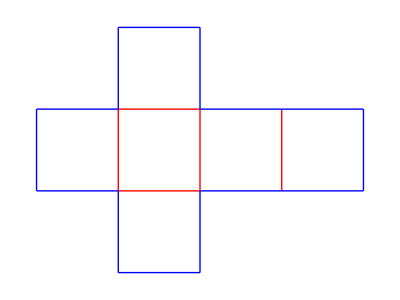
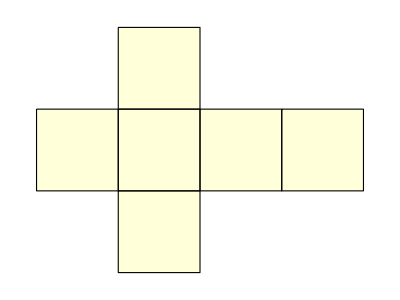
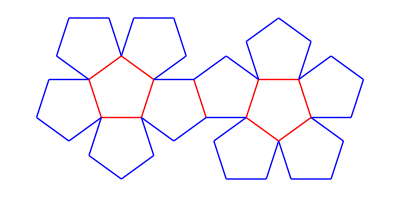
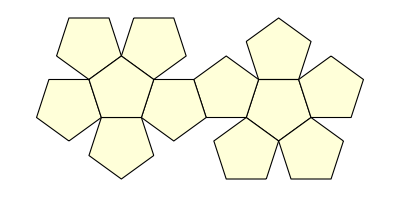
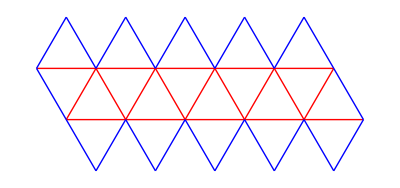
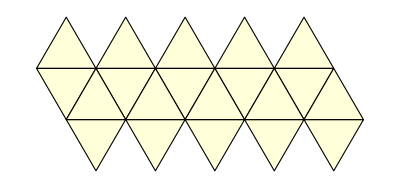
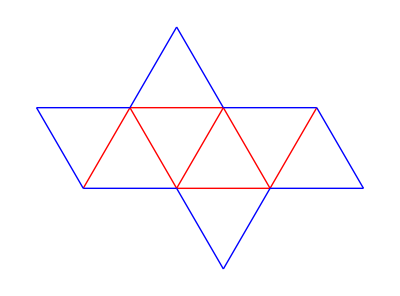
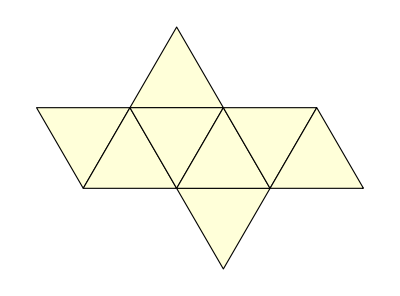
Cube-Graphics--Graphics-
Dodecahedron-Graphics--Graphics-
Icosahedron-Graphics--Graphics-
Octahedron-Graphics--Graphics-
Tetrahedron-Graphics--Graphics-
Cuboctahedron-Graphics--Graphics-
GreatRhombicosidodecahedron-Graphics--Graphics-
GreatRhombicuboctahedron-Graphics--Graphics-
Icosidodecahedron-Graphics--Graphics-
SmallRhombicosidodecahedron-Graphics--Graphics-
SmallRhombicuboctahedron-Graphics--Graphics-
SnubCube-Graphics--Graphics-
SnubDodecahedron-Graphics--Graphics-
TruncatedCube-Graphics--Graphics-
TruncatedDodecahedron-Graphics--Graphics-
TruncatedIcosahedron-Graphics--Graphics-
TruncatedOctahedron-Graphics--Graphics-
TruncatedTetrahedron-Graphics--Graphics-
DeltoidalHexecontahedron-Graphics--Graphics-
DeltoidalIcositetrahedron-Graphics--Graphics-
DisdyakisDodecahedron-Graphics--Graphics-
DisdyakisTriacontahedron-Graphics--Graphics-
PentagonalHexecontahedron-Graphics--Graphics-
PentagonalIcositetrahedron-Graphics--Graphics-
PentakisDodecahedron-Graphics--Graphics-
RhombicDodecahedron-Graphics--Graphics-
RhombicTriacontahedron-Graphics--Graphics-
SmallTriakisOctahedron-Graphics--Graphics-
TetrakisHexahedron-Graphics--Graphics-
TriakisIcosahedron-Graphics--Graphics-
TriakisTetrahedron-Graphics--Graphics-
MathematicaPolyhedron-Graphics--Graphics-
ElongatedDodecahedron-Graphics--Graphics-

```mathematica
Column[
Function[poly,
Row[{poly,
{points, outsideBorder, outsideBorderDegrees, insideEdges} = outline[poly];
Graphics[
{Red, GraphicsComplex[points,Line[insideEdges]], Blue, GraphicsComplex[points,Line[outsideBorder]]}, 
Axes -> False
],
PolyhedronData[poly, "NetImage"]}
] (* row *)
] /@Flatten[{PolyhedronData["Platonic"],PolyhedronData["Archimedean"], PolyhedronData["ArchimedeanDual"], "MathematicaPolyhedron", "ElongatedDodecahedron"}]
](* column *)
```